◼ "\◼ "2023-11-11T01:47v1 .20M. J. Steil[msteil@theorie.ikp.physik.tu-darmstadt.de](mailto:msteil@theorie.ikp.physik.tu-darmstadt.de)TU Darmstadt

# Computational fluid dynamic

Martin Jakob Steil^1

^1Technische Universität Darmstadt

Abstract

Initialization

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
$DistributedContexts={};

(* Disable Notebookhistory, [https://mathematica.stackexchange.com/questions/11258/are-there-suitable-versioning-systems-for-mathematica-notebooks]*)
SetOptions[EvaluationNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},System`TrackCellChangeTimes->False]

(* Display the Timing of an Evaluation in a Notebook Window [https://reference.wolfram.com/language/howto/DisplayTheTimingOfAnEvaluationInANotebookWindow.html] *)
SetOptions[EvaluationNotebook[],EvaluationCompletionAction->{"ShowTiming"}]
```

```mathematica
Needs["CompiledFunctionTools`"]

(* provides ColorData["Plasma"] and ColorData["Viridis"] from Python matplotlib package *)
Get["D:/Github/Mathematica/Packages/PythonColorMaps/PythonColorMaps.m"];

HeavisideThetaN[x_]:=Piecewise[{{0,x<=0},{1,x>0}}]

Unprotect[ParallelTable];
Options[ParallelTable]={DistributedContexts:>All,Method->"FinestGrained",ProgressReporting:>True};
Protect[ParallelTable];

colors=ColorData[97, "ColorList"];
```

Set::write: Tag ParallelTable in Options[ParallelTable] is Protected.

(** Update embedded Stylesheet **)
Needs["StylesheetTools`","D:/Github/Mathematica/Packages/StylesheetTools/StylesheetTools.m"];
style=GetStyleDefinitions[];
files=FileNames["D:\Desktop\PhD-Thesis\appendix\*.nb"];
SetStyleDefinitions[files,style];

### Tagged Methods

(** Update tagged methods **)
Needs["UpdateTaggedMethod`","D:/Github/Mathematica/Packages/UpdateTaggedMethod/UpdateTaggedMethod.m"];
UpdateTaggedMethods["D:/Github/Mathematica/tagged_methods.nb"]

```mathematica
(* SaveToCell | v2.0 | Save assigned value of symbol(s) to cell(s) | Modified Version of [http://szhorvat.net/pelican/save-data-in-notebooks.html] *)
ClearAll[SaveToCell];
SaveToCell[names_/;VectorQ[names,StringQ],suffix:Except[_?OptionQ]:"",comment:Except[_?OptionQ]:"",opt:OptionsPattern[]]:=Module[{
	data=Symbol[#]&/@names,
	label=Row[Flatten@{If[comment=!="",{Style[comment,Plain],", "},Nothing],DateString["ISODateTime"]}]
	},
	CellPrint@Cell[
		BoxData@MapThread[RowBox[{#2<>suffix,"=",ToBoxes[Iconize[#1,label,Method->Compress]],";"}]&,{data,names}],
		"Input",
		GeneratedCell->False,(*prevent deletion by Cell>Delete All Output:*)
		CellLabel->"(saved)",
		CellLabelAutoDelete->False,
		opt
	]
]

SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"",comment:Except[_?OptionQ]:"",opt:OptionsPattern[]]:=With[{
	data=Evaluate[var],
	label=Row[Flatten@{If[comment=!="",{Style[comment,Plain],", "},Nothing],DateString["ISODateTime"]}]
	},
	CellPrint@Cell[
		BoxData@RowBox[{If[name=!="",name,MakeBoxes[var]],"=",ToBoxes[Iconize[data,label,Method->Compress]],";"}],
		"Input",
		GeneratedCell->False,(*prevent deletion by Cell>Delete All Output:*)
		CellLabel->"(saved)",
		CellLabelAutoDelete->False,
		opt
	]
]
SaveToCell::usage="SaveToCell[var_,name:Except[_?OptionQ]:\"\",comment:Except[_?OptionQ]:\"\",opt:OptionsPattern[]]: saves the assignment of var/or the data in\
 var (under name if name=!=\"\") in a compressed iconized form with a label including comment and a time stamp.\n\
SaveToCell[names_/;VectorQ[names,StringQ],suffix_:Except[_?OptionQ]:\"\",comment:Except[_?OptionQ]:\"\",opt:OptionsPattern[]]: saves the assignments behind the elements of names in\
 in a compressed iconized form with suffix appended to the symbol names and a label including comment and a time stamp.";
```

```mathematica
(* AutoCollapse | v2.0 | Close CellGroup | [https://mathematica.stackexchange.com/a/683] *)
AutoCollapse[]:=Module[{},
	If[$FrontEnd=!=$Failed,
		SelectionMove[EvaluationNotebook[],All,GeneratedCell];
		FrontEndTokenExecute["SelectionCloseUnselectedCells"]
	];
]
AutoCollapse::usage="Collapse input cells by grouping them with the generated output cells.";
```

```mathematica
(* CellPrintDisplayFormulaNumbered | v2.2 | CellPrint a DisplayFormulaNumbered *)
ClearAll[CellPrintDisplayFormulaNumbered,CellPrintDisplayFormulaNumberedNAC];
CellPrintDisplayFormulaNumbered[exp_,tag_:None,comment_:"",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:True]:=Module[{frameLabels,box},
	frameLabels=CellFrameLabels->{
		{None,Cell[TextData[{If[tag===None,"",ToString[tag]<>" "]<>"(",CounterBox["Chapter"],".",CounterBox["DisplayFormulaNumbered"],")"}],"DisplayFormulaEquationNumber"]},
		{None,None}
	};
	box=BoxData[RowBox[{ToBoxes[exp],RowBox[{comment}]}]];
	CellPrint[Cell[box,"DisplayFormulaNumberedPrinted",frameLabels,
		GeneratedCell->generatedCellQ,CellAutoOverwrite->True,ShowStringCharacters->False,CellGroupingRules->If[groupQ,"OutputGrouping",Inherited]]
	];
	If[autoCollapseQ,AutoCollapse[]];
]
CellPrintDisplayFormulaNumbered::usage="CellPrintDisplayFormulaNumbered[exp_,tag_:None,comment_:\"\",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:True]:\
CellPrint exp to a DisplayFormulaNumberedPrinted output cell.";
CellPrintDisplayFormulaNumberedNAC[exp_,tag_:None,comment_:"",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:False]:=CellPrintDisplayFormulaNumbered[exp,tag,comment,generatedCellQ,groupQ,autoCollapseQ]
CellPrintDisplayFormulaNumbered::usage="Same as CellPrintDisplayFormulaNumbered[] but autoCollapseQ defaults to false.";
```

```mathematica
(* ListDensityContourPlot | v1.0 |  *)
ClearAll[ListDensityContourPlot];
Options[ListDensityContourPlot]=Join[Options[ListDensityPlot],Map[#->OptionValue[ListContourPlot,#]&,{ContourLabels,ContourLines,Contours,ContourShading,ContourStyle}]];
ListDensityContourPlot[data_,OptionsPattern[]]:=With[{
	contourOptions=Map[#->OptionValue[ListDensityContourPlot,#]&,Options[ListContourPlot][[All,1]]]/.{
		Rule[PlotLegends,x_]:>Rule[PlotLegends,None],Rule[ColorFunction,x_]:>Rule[ColorFunction,Opacity[0]&]},
	densityOptions=Map[#->OptionValue[ListDensityContourPlot,#]&,Options[ListDensityPlot][[All,1]]]},
	If[OptionValue[ListDensityContourPlot,Contours]===0,
		Return@Show[{ListDensityPlot[data,##]&@@densityOptions}];,
		(*else*)
		Return@Show[{ListDensityPlot[data,##]&@@densityOptions,ListContourPlot[data,##]&@@contourOptions}]
	];
]
ListDensityContourPlot::usage="ListDensityContourPlot[data_,OptionsPattern[]]: A simple wrapper to create a ListDensityPlot of `data` with given options overlayed\
with a ListContourPlot with given options (e.g. Contour->10) but no own coloring between contours.";
```

## Kurganov-Tadmor (central) [KT] and Kurganov-Petrova-Popov (central upwind) [KNP] MUSCL Scheme

Implementation of expressions from Subsection  2.2.2 “The KT/KNP scheme and the \MUSCL reconstruction” [M. J. Steil, - 2023 - PhD thesis]

Semi-discrete O(Δx^2) finite volume method, implemented in one spatial dimension for single component system, MUSCL reconstruction for advection Flux using minmod-limiter, implement for PDEs of the type:

∂_t u[t,x]+d_x F[t,x,u,pars]==d_x Q[t,x,u,∂_x u,pars]+S[t,x,u,pars]+∂_x s[t,x,u,pars]
IC: U[0,x]=∫_x_0^x dy u[0,y]
BC: Reconstruction of ghost cells u_-2, u_-1 on left boundary and u_(n-1), u_(n-2) 

d_x F[t,x,u,pars]: Advection term
d_x Q[t,x,u,∂_x u,pars]: Diffusion term
S[t,x,u,pars]: Source term
s[t,x,u,pars]: Internal source term — special case of a source term since ∂_x s[t,x,u,pars] may be considered as a conventional source S[t,x,u,pars]

## KT flux limiters

```mathematica
(** Selected MUSCL scheme Flux limiter [https://en.wikipedia.org/wiki/Flux_limiter] **)
KT`ϕ`MinMod=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,1.,Max[0.,Min[1.,Δuj/Δujp1]]]]; (* MinMod Limiter [https://en.wikipedia.org/wiki/Flux_limiter] *)
KT`ϕ`GeneralizedMinMod[θ_]/;1<=θ≤2:=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,θ,With[{r=Δuj/Δujp1},Max[0.,Min[θ r,0.5*(1+r),θ]]]]];

KT`ϕ`VanAlbada1=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,1.,With[{r=Δuj/Δujp1},r(r+1.)/(r*r+1.)]]];
KT`ϕ`VanLeer=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,2.,With[{r=Δuj/Δujp1},(r+Abs[r])/(1+Abs[r])]]];
KT`ϕ`MonotonizedCentral=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,2.,With[{r=Δuj/Δujp1},Max[0.,Min[2r,0.5*(1+r),2.]]]]];
KT`ϕ`Koren=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,2.,With[{r=Δuj/Δujp1},Max[0.,Min[2r,Min[(1.+2.*r)/3.,2.]]]]]];
KT`ϕ`Superbee=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,2.,With[{r=Δuj/Δujp1},Max[0.,Min[2.r,1.],Min[r,2.]]]]];

KT`ϕ`CHARM=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,3.,With[{r=Δuj/Δujp1},If[r≤0,0.,r(3r+1)/(r+1.)^2]]]](* Not TVD *);
KT`ϕ`HCUS=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,3.,With[{r=Δuj/Δujp1},1.5*(r+Abs[r])/(r+2.)]]](* Not TVD *);
KT`ϕ`HQUICK=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,4.,With[{r=Δuj/Δujp1},2.0*(r+Abs[r])/(r+3.)]]](* Not TVD *);

KT`ϕ`VanAlbada2=Function[{Δuj,Δujp1},If[Abs@Δujp1==0.,0.,With[{r=Δuj/Δujp1},2.*r/(r*r+1.)]]](* Not TVD *);
```

KT`TVDregion=Show[{
	RegionPlot[(ϕ<=2r&&ϕ>=r&&ϕ≤1)||(r>=1&&ϕ≥1&&ϕ≤2&&ϕ<=r),{r,0,4},{ϕ,0,3},
		PlotRange→{{0,4},{0,3}},PlotPoints→50,MaxRecursion→4,
		FrameLabel→{"r","ϕ(r)"},	PlotLegends→Placed[{"TVD region"},{Right,Bottom}],
		PlotStyle→Blend[{White,Black},1/6],BoundaryStyle->None,AspectRatio→3/4
	],
	Graphics[{Arrowheads[0.03],Arrow[{{6/4,3/4},{6/4,3/4-1/2}}],Text["   increasing dissipativity",{6/4,3/4-1/4},{-1,0}]}],
	Graphics[{Arrowheads[0.03],Arrow[{{6/4,2+1/4},{6/4,2+3/4}}],Text["   decreasing dissipativity",{6/4,2+2/4},{-1,0}]}]
}];
Show[{
	KT`TVDregion,
	Plot[{
		KT`ϕ`MinMod[r,1],KT`ϕ`VanAlbada1[r,1],KT`ϕ`VanLeer[r,1],
		KT`ϕ`MonotonizedCentral[r,1],KT`ϕ`Koren[r,1],KT`ϕ`Superbee[r,1],
		KT`ϕ`VanAlbada2[r,1],KT`ϕ`CHARM[r,1],KT`ϕ`HCUS[r,1],KT`ϕ`HQUICK[r,1]
		},{r,0,4},
		PlotStyle→AbsoluteThickness[2],
		PlotRange→All,PlotLegends→Placed[{"MinMod","van Albada 1","van Leer","Monotonized Central","Koren","Superbee","van Albada 2","CHARM","HCUS","HQUICK"},{Left,Top}]
	]},ImageSize→500
]

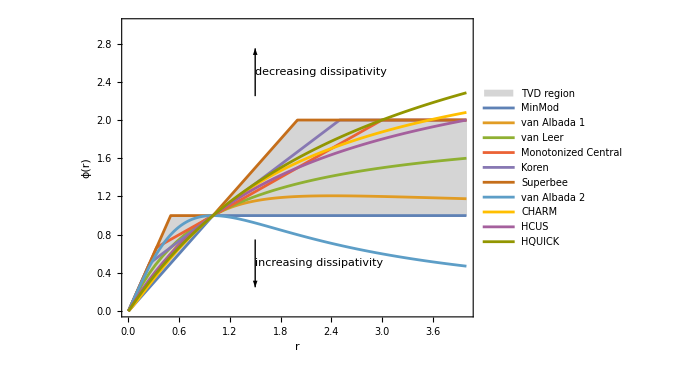

## KT Boundary conditions

```mathematica
(** Selected ghost cell reconstructions implementing certain boundary conditions **)
KT`bc`ASLE=Function[{vin},Module[{v},
	v=vin;
	v[[1]]=-v[[5]];(* Subscript[u, -2] = -Subscript[u, 2] *)
	v[[2]]=-v[[4]];(* Subscript[u, -1] = -Subscript[u, 1] *)
	v[[3]]=0*v[[3]]; (* Subscript[u, 0] = 0 *)
	v[[-2]]=2v[[-3]]-v[[-4]];(* Subscript[u, n] = 2 Subscript[u, n-1] - Subscript[u, n-2]*)
	v[[-1]]=3v[[-3]]-2v[[-4]];(* Subscript[u, n+1]= 3 Subscript[u, n-1] - 2 Subscript[u, n-2]*)
	v
]];(* Antisymmetric BC at Subscript[x, 0] and linear extrapolation at Subscript[x, n-1] *)

KT`bc`LELE=Function[{vin},Module[{v},
	v=vin;
	v[[1]]=3v[[3]]-2v[[4]];(* Subscript[u, -2] = 3 Subscript[u, 0] - 2 Subscript[u, 1]*)
	v[[2]]=2v[[3]]-v[[4]];(* Subscript[u, -1] = 2 Subscript[u, 0] - Subscript[u, 1]*)
	v[[-2]]=2v[[-3]]-v[[-4]];(* Subscript[u, n] = 2 Subscript[u, n-1] - Subscript[u, n-2]*)
	v[[-1]]=3v[[-3]]-2v[[-4]];(* Subscript[u, n+1]= 3 Subscript[u, n-1] - 2 Subscript[u, n-2]*)
	v
]];(* Linear extrapolation at Subscript[x, 0] and Subscript[x, n-1] *)

KT`bc`periodic=Function[{vin},Module[{v},
	v=vin;
	v[[1]]=v[[-5]];(* Subscript[u, -2]= Subscript[u, n-3] *)
	v[[2]]=v[[-4]];(* Subscript[u, -1]= Subscript[u, n-2] *)
	v[[-3]]=v[[3]];(* Subscript[u, n-1]= Subscript[u, 0] *)
	v[[-2]]=v[[4]];(* Subscript[u, n] = Subscript[u, 1] *)
	v[[-1]]=v[[5]];(* Subscript[u, n+1] = Subscript[u, 2] *)
	v
]];

KT`bc`antiperiodic=Function[{vin},Module[{v},
	v=vin;
	v[[1]]=-v[[-5]];(* Subscript[u, -2]= -Subscript[u, n-3] *)
	v[[2]]=-v[[-4]];(* Subscript[u, -1]= -Subscript[u, n-2] *)
	v[[-3]]=-v[[3]];(* Subscript[u, n-1]= -Subscript[u, 0] *)
	v[[-2]]=-v[[4]];(* Subscript[u, n] = -Subscript[u, 1] *)
	v[[-1]]=-v[[5]];(* Subscript[u, n+1] = -Subscript[u, 2] *)
	v
]];

KT`bc`vectorize[bc_]:=bc/.HoldPattern[Part[x_,i_]]:>Part[x,All,i]
```

## KT`stepper

### KT`O2rec — MUSCL Reconstruction

```mathematica
ClearAll[KT`O2rec];

(** MUSCL reconstruction **)
KT`O2rec[ϕ_:KT`ϕ`MinMod,uxFilter_:Identity][0]:=Compile[{{u,_Real,1},{Δu,_Real,1}},
	Module[{
		ux,(* Reconstructed slopes: Subscript[(Subscript[u, x]), i]=0.5*(Subscript[u, i+1]-Subscript[u, i])*ϕ[Subscript[u, i]-Subscript[u, i-1],Subscript[u, i+1]-Subscript[u, i]^j], dim =nx+2 *)
		up12,(* Right intermediate values at the cell interface Subscript[x, i+1/2]: Subscript[u, i+1/2]^+=Subscript[u, i+1]-Subscript[(Subscript[u, x]), i+1], dim =nx+1 *)
		um12(* Left intermediate values at the cell interface Subscript[x, i+1/2]: Subscript[u, i+1/2]^-=Subscript[u, i]+Subscript[(Subscript[u, x]), i], dim=nx+1 *)
	},
		ux=uxFilter[MapThread[0.5*#2(ϕ[#1,#2])&,{Take[#,{1,-2}],Take[#,{2,-1}]}]]&@Δu;
		(* [KTO2-0, eq. (2.4)*0.5*Δx]: modified to be compatible with generic
		flux limiters from [https://en.wikipedia.org/wiki/Flux_limiter], see also [https://en.wikipedia.org/wiki/MUSCL_scheme] *)														
		
		up12=Take[u,{3,-2}]-Take[ux,{2,-1}];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters *)
		um12=Take[u,{2,-3}]+Take[ux,{1,-2}];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters *)
		Return[{up12,um12}]
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]

(** MUSCL reconstruction for vector valued conserved quantities**)
KT`O2rec[ϕ_:KT`ϕ`MinMod,uxFilter_:Identity][nu_/;nu=!=0]:=Compile[{{u,_Real,2},{Δu,_Real,2}},
	Module[{
		ux,(* Reconstructed derivatives Subscript[(Subscript[u, x]^j), i]=0.5*(Subscript[u, i+1]^j-Subscript[u, i]^j)*ϕ[Subscript[u, i]^j-Subscript[u, i-1]^j,Subscript[u, i+1]^j-Subscript[u, i]^j], dim =nu*(nx+2) *)
		up12T,(* Reconstructed slopes {Subscript[u, i+1/2]^(j,+)}=Subscript[u, i+1]^j-Subscript[(Subscript[u, x]^j), i+1], dim =(nx+1)*nu, (T): values at constant Subscript[x, i+1/2] are grouped *)
		um12T(* Reconstructed slopes {Subscript[u, i+1/2]^(j,-)}=Subscript[u, i]^j+Subscript[(Subscript[u, x]^j), i], dim =(nx+1)*nu, (T) *)
	},
		ux=uxFilter[MapThread[0.5*#2(ϕ[#1,#2])&,{Take[#,{1,-2}],Take[#,{2,-1}]}]]&/@Δu;
		(* [KTO2-0, eq. (2.4)*0.5*Δx]: modified to be compatible with generic 
		flux limiters from [https://en.wikipedia.org/wiki/Flux_limiter], see also [https://en.wikipedia.org/wiki/MUSCL_scheme] *)
																									
		up12T=Transpose[(Take[#,{3,-2}]&/@u)-(Take[#,{2,-1}]&/@ux)];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters *)
		um12T=Transpose[(Take[#,{2,-3}]&/@u)+(Take[#,{1,-2}]&/@ux)];(* [KTO2-0, eq. (4.5)]: modified to be compatible with generic flux limiters *)
		Return[{up12T,um12T}]
		
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]
```

### KT`O1rec — First order Reconstruction

```mathematica
ClearAll[KT`O1rec];

KT`O1rec[opts___][0]:=KT`O2rec[0&][0]
KT`O1rec[opts___][nu_/;nu=!=0]:=KT`O2rec[0&][nu]
```

### KT`H12 — Advection flux for F[t,x,u,pars]

```mathematica
ClearAll[KT`H12];

KT`H12[F_Function,dFdu_Function,pars___][nx_,0][Δx_,x_,x12_]:=Compile[{{t,_Real},{up12,_Real,1},{um12,_Real,1},{dudt0,_Real,1}},
	Module[{
		λp12, (* Jacobian eigenvalues (single value) at Subscript[x, i+1/2] using Subscript[u, i+1/2]^+: Subscript[λ, i+1/2]^+=dFdu[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+,params], dim=nx+1 *)
		λm12, (* Jacobian eigenvalues (single value) at Subscript[x, i+1/2] using Subscript[u, i+1/2]^-: Subscript[λ, i+1/2]^-=dFdu[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-,params], dim=nx+1 *)
		a12,(* Approxmiate local speed at Subscript[x, i+1/2]: Subscript[a, i+1/2]=Max[Abs@Subscript[λ, i+1/2]^+,Abs@Subscript[λ, i+1/2]^-], dim=nx+1 *)
		Fp12,(* Flux through Subscript[x, i+1/2] using Subscript[u, i+1/2]^+: Subscript[F, i+1/2]^+=F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+,params], dim=nx+1 *)
		Fm12,(* Flux through Subscript[x, i+1/2] using Subscript[u, i+1/2]^-: Subscript[F, i+1/2]^-=F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-,o,params], dim=nx+1 *)
		H12(* Advection fluxes through Subscript[x, i+1/2]: Subscript[H, i+1/2]=... , dim=nx+1 *)
	},
		λp12=MapThread[dFdu[t,#1,#2,pars]&,{x12,up12}];
		λm12=MapThread[dFdu[t,#1,#2,pars]&,{x12,um12}];
		a12=MapThread[Max[Abs@#1,Abs@#2]&,{λp12,λm12}]; (* [KTO2-0, eq. (3.2)] [KTO2-0, footnote 2] *)
	
		Fp12=MapThread[F[t,#1,#2,pars]&,{x12,up12}];
		Fm12=MapThread[F[t,#1,#2,pars]&,{x12,um12}];
		H12=0.5*(Fp12+Fm12-a12*(up12-um12));
		
		(* [KTO2-0, eq. (4.4)]:  {Subscript[H, i+1/2]}=(F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+]+F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-])/2-Subscript[a, i+1/2]/2(Subscript[u, i+1/2]^+-Subscript[u, i+1/2]^-) *)
		Return[-Differences[H12]/Δx]		
		
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]

KT`H12[F_Function,dFdu_Function,pars___][nx_,nu_/;nu=!=0][Δx_,x_,x12_]:=Compile[{{t,_Real},{up12T,_Real,2},{um12T,_Real,2},{dudt0,_Real,2}},
	Module[{
		λp12T, (* Jacobian eigenvalues at Subscript[x, i+1/2]: {Subscript[λ, i+1/2]^(j,+)}=λdFdu[t,{Subscript[u, i+1/2]^(j,+)},params], dim =(nx+1)*nu, (T) *)
		λm12T, (* Jacobian eigenvalues at Subscript[x, i+1/2]: {Subscript[λ, i+1/2]^(j,-)}=λdFdu[t,{Subscript[u, i+1/2]^(j,-)},params], dim =(nx+1)*nu, (T) *)
		a12T,(* Approxmiate velocities at Subscript[x, i+1/2]: Subscript[a, i+1/2]=Max[Max@Abs@Subscript[λ, i+1/2]^+,Max@Abs@Subscript[λ, i+1/2]^-], dim =(nx+1)*1, *)
		Fp12T,(* Flux through Subscript[x, i+1/2] using {Subscript[F, i+1/2]^(j,+)}=F[t,Subscript[x, i+1/2],{Subscript[u, i+1/2]^(j,+)},params], dim =(nx+1)*nu, (T) *)
		Fm12T,(* Flux through Subscript[x, i+1/2] using {Subscript[F, i+1/2]^(j,-)}=F[t,Subscript[x, i+1/2],{Subscript[u, i+1/2]^(j,-)},params], dim =(nx+1)*nu, (T) *)
		H12(* Advection fluxes through Subscript[x, i+1/2], {{Subscript[H, i+1/2]^0},...,{Subscript[H, i+1/2]^(nu-1)}}=... , dim = nu*(nx+1) *)
	},
		λp12T=MapThread[dFdu[t,#1,#2,pars]&,{x12,up12T}];
		λm12T=MapThread[dFdu[t,#1,#2,pars]&,{x12,um12T}];
		a12T=MapThread[Max[Max@Abs@#1,Max@Abs@#2]&,{λp12T,λm12T}]; (* [KTO2-0, eq. (3.2)] [KTO2-0, footnote 2] *)
		
		Fp12T=MapThread[F[t,#1,#2,pars]&,{x12,up12T}];
		Fm12T=MapThread[F[t,#1,#2,pars]&,{x12,um12T}];

		H12=Transpose[0.5*(Fp12T+Fm12T-a12T*(up12T-um12T))]; 
		(* [KTO2-0, eq. (4.4)]:  {{Subscript[H, i+1/2]^0},...,{Subscript[H, i+1/2]^(nu-1)}}ᵀ={Subscript[H, i+1/2]^j}ᵀ=(F[t,Subscript[x, i+1/2],{Subscript[u, i+1/2]^(j,+)}]+F[t,Subscript[x, i+1/2],{Subscript[u, i+1/2]^(j,-)}])/2-Subscript[a, i+1/2]/2({Subscript[u, i+1/2]^(j,+)}-{Subscript[u, i+1/2]^(j,-)}) *)
		
		Return[(-Differences[#]/Δx)&/@H12]
				
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]
```

### KNP`H12 — Advection flux for F[t,x,u,pars]

```mathematica
ClearAll[KNP`H12];

KNP`H12[F_Function,dFdu_Function,pars___][nx_,0][Δx_,x_,x12_]:=Compile[{{t,_Real},{up12,_Real,1},{um12,_Real,1},{dudt0,_Real,1}},
	Module[{
		λp12, (* Jacobian eigenvalues (single value) at Subscript[x, i+1/2] using Subscript[u, i+1/2]^+: Subscript[λ, i+1/2]^+=dFdu[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+,params], dim=nx+1 *)
		λm12, (* Jacobian eigenvalues (single value) at Subscript[x, i+1/2] using Subscript[u, i+1/2]^-: Subscript[λ, i+1/2]^-=dFdu[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-,params], dim=nx+1 *)
		a12,(* Approxmiate local speed at Subscript[x, i+1/2]: Subscript[a, i+1/2]=Max[Abs@Subscript[λ, i+1/2]^+,Abs@Subscript[λ, i+1/2]^-], dim=nx+1 *)
		ap12,(* Approxmiate velocities at Subscript[x, i+1/2]: Subscript[a, i+1/2]^+=Max[Subscript[λ, i+1/2]^+,Subscript[λ, i+1/2]^-,0], dim =(nx+1) *)
		am12,(* Approxmiate velocities at Subscript[x, i+1/2]: Subscript[a, i+1/2]^-=Min[Subscript[λ, i+1/2]^+,Subscript[λ, i+1/2]^-,0], dim =(nx+1) *)
		Fp12,(* Flux through Subscript[x, i+1/2] using Subscript[u, i+1/2]^+: Subscript[F, i+1/2]^+=F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^+,params], dim=nx+1 *)
		Fm12,(* Flux through Subscript[x, i+1/2] using Subscript[u, i+1/2]^-: Subscript[F, i+1/2]^-=F[t,Subscript[x, i+1/2],Subscript[u, i+1/2]^-,o,params], dim=nx+1 *)
		H12(* Advection fluxes through Subscript[x, i+1/2]: Subscript[H, i+1/2]=... , dim=nx+1 *)
	},
		λp12=MapThread[dFdu[t,#1,#2,pars]&,{x12,up12}];
		λm12=MapThread[dFdu[t,#1,#2,pars]&,{x12,um12}];
		ap12=MapThread[Max[#1,#2,0]&,{λp12,λm12}]; (* [KTO2-1, eq. (3.2)] [KTO2-0, footnote 2] *)
		am12=MapThread[Min[#1,#2,0]&,{λp12,λm12}]; (* [KTO2-1, eq. (3.2)] [KTO2-0, footnote 2] *)
			
		Fp12=MapThread[F[t,#1,#2,pars]&,{x12,up12}];
		Fm12=MapThread[F[t,#1,#2,pars]&,{x12,um12}];
		H12=(ap12*Fm12-am12*Fp12+ap12*am12*(up12-um12))/(ap12-am12+$MachineEpsilon);
		(* [KTO2-1, eq. (3.15)]: {Subscript[H, i+1/2]}=(Subscript[a, j+1/2]^+F[Subscript[u, j+1/2]^-]-Subscript[a, j+1/2]^-F[Subscript[u, j+1/2]^+])/(Subscript[a, j+1/2]^+-Subscript[a, j+1/2]^-)+(Subscript[a, j+1/2]^+Subscript[a, j+1/2]^-)/(Subscript[a, j+1/2]^+-Subscript[a, j+1/2]^-)(Subscript[u, j+1/2]^+-Subscript[u, j+1/2]^-) *)
		Return[-Differences[H12]/Δx]		
		
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]


KNP`H12[F_Function,dFdu_Function,pars___][nx_,nu_/;nu=!=0][Δx_,x_,x12_]:=Compile[{{t,_Real},{up12T,_Real,2},{um12T,_Real,2},{dudt0,_Real,2}},
	Module[{
		λp12T, (* Jacobian eigenvalues at Subscript[x, i+1/2]: {Subscript[λ, i+1/2]^(j,+)}=λdFdu[t,{Subscript[u, i+1/2]^(j,+)},params], dim =(nx+1)*nu, (T) *)
		λm12T, (* Jacobian eigenvalues at Subscript[x, i+1/2]: {Subscript[λ, i+1/2]^(j,-)}=λdFdu[t,{Subscript[u, i+1/2]^(j,-)},params], dim =(nx+1)*nu, (T) *)
		ap12T, (* Approxmiate velocities at Subscript[x, i+1/2]: Subscript[a, i+1/2]^+=Max[Max@Subscript[λ, i+1/2]^+,Max@Subscript[λ, i+1/2]^-,0], dim =(nx+1)*1, (T) *)
		am12T, (* Approxmiate velocities at Subscript[x, i+1/2]: Subscript[a, i+1/2]^-=Min[Min@Subscript[λ, i+1/2]^+,Min@Subscript[λ, i+1/2]^-,0], dim =(nx+1)*1, (T) *)
		Fp12T,(* Flux through Subscript[x, i+1/2] using {Subscript[F, i+1/2]^(j,+)}=F[t,Subscript[x, i+1/2],{Subscript[u, i+1/2]^(j,+)},params], dim =(nx+1)*nu, (T) *)
		Fm12T,(* Flux through Subscript[x, i+1/2] using {Subscript[F, i+1/2]^(j,-)}=F[t,Subscript[x, i+1/2],{Subscript[u, i+1/2]^(j,-)},params], dim =(nx+1)*nu, (T) *)
		H12(* Advection fluxes through Subscript[x, i+1/2], {{Subscript[H, i+1/2]^0},...,{Subscript[H, i+1/2]^(nu-1)}}=... , dim = nu*(nx+1) *)
	},
		λp12T=MapThread[dFdu[t,#1,#2,pars]&,{x12,up12T}];
		λm12T=MapThread[dFdu[t,#1,#2,pars]&,{x12,um12T}];
		ap12T=MapThread[Max[Max@#1,Max@#2,0]&,{λp12T,λm12T}]; (* [KTO2-1, eq. (3.2)] [KTO2-0, footnote 2] *)
		am12T=MapThread[Min[Min@#1,Min@#2,0]&,{λp12T,λm12T}]; (* [KTO2-1, eq. (3.2)] [KTO2-0, footnote 2] *)
		
		Fp12T=MapThread[F[t,#1,#2,pars]&,{x12,up12T}];
		Fm12T=MapThread[F[t,#1,#2,pars]&,{x12,um12T}];

		H12=Transpose[(ap12T*Fm12T-am12T*Fp12T+ap12T*am12T*(up12T-um12T))/(ap12T-am12T+$MachineEpsilon)]; 
		(* [KTO2-0, eq. (4.4)]:  {{Subscript[H, i+1/2]^0},...,{Subscript[H, i+1/2]^(nu-1)}}ᵀ={Subscript[H, i+1/2]^j}ᵀ=(F[t,Subscript[x, i+1/2],{Subscript[u, i+1/2]^(j,+)}]+F[t,Subscript[x, i+1/2],{Subscript[u, i+1/2]^(j,-)}])/2-Subscript[a, i+1/2]/2({Subscript[u, i+1/2]^(j,+)}-{Subscript[u, i+1/2]^(j,-)}) *)
		
		Return[(-Differences[#]/Δx)&/@H12]
				
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]
```

### KT`O2P12 — Diffusion flux for Q[t,x,u,dudx,pars]

```mathematica
ClearAll[KT`O2P12];

KT`O2P12[Q_Function,pars___][nx_,0][Δx_,x_,x12_]:=Compile[{{t,_Real},{u,_Real,1},{Δu,_Real,1},{dudt0,_Real,1}},
	Module[{
		dudx, (* Aproximate derivatives of conserved quantity: {Subscript[u, 0]-Subscript[u, -1],...,Subscript[u, nx-1]-Subscript[u, nx-2],Subscript[u, nx]-Subscript[u, nx-1]}/Δx, dim=nx+1 *)
		P12(* Diffusion flux through Subscript[x, i+1/2]: Subscript[P, i+1/2]=... , dim =nx+1 *)
	},
		dudx=Take[Δu,{2,-2}]/Δx;
		P12=0.5*MapThread[Q[t,#1,#3,#5,pars]+Q[t,#2,#4,#5,pars]&,{
			Join[{x12[[1]]-Δx*0.5},x],(* =Subscript[x, i+1/2]-Δx/2={Subscript[x, -1],{Subscript[x, i]}}≡{Subscript[x̂, i]}, contains cell center of second ghost cell [Subscript[x, -3/2],Subscript[x, -1/2]] *)
			Join[x,{x12[[-1]]+Δx*0.5}],(* =Subscript[x, i+1/2]+Δx/2={{Subscript[x, i]},Subscript[x, n]}≡{Subscript[x̂, i+1]}, contains cell center of penultimate ghost cell [Subscript[x, n-1/2],Subscript[x, n+1/2]] *)
			Take[u,{2,-3}], (* =Subscript[u, i] *)
			Take[u,{3,-2}],(* =Subscript[u, i+1] *)
			dudx(* =(Subscript[u, i+1]-Subscript[u, i])/Δx *)
		}]; 
		(* [KTO2-0, eq. (4.14)]: {Subscript[P, i+1/2]}=1/2(Q[t,Subscript[x̂, i],Subscript[u, i],(Subscript[u, i+1]-Subscript[u, i])/Δx]+Q[t,Subscript[x̂, i+1],Subscript[u, i+1],(Subscript[u, i+1]-Subscript[u, i])/Δx]) *)
		Return[Differences[P12]/Δx]		
		
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]
KT`O2P12[Q_Function,pars___][nx_,nu_/;nu=!=0][Δx_,x_,x12_]:=Compile[{{t,_Real},{u,_Real,2},{Δu,_Real,2},{dudt0,_Real,2}},
	Module[{
		uT,(* Conserved quanties: {{Subscript[u, -1]^0,...,Subscript[u, -1]^(nu-1)},{Subscript[u, 0]^0,...,Subscript[u, 0]^(nu-1)},...,{Subscript[u, nx-1]^0,...,Subscript[u, nx-1]^(nu-1)},{Subscript[u, nx]^0,...,Subscript[u, nx]^(nu-1)}} ,dim=(nx+2)*nu, (T) *)
		dudxT,(* Approximate derivatives: {{Subscript[u, 0]^0-Subscript[u, -1]^0,...,Subscript[u, 0]^(nu-1)-Subscript[u, -1]^(nu-1)},...,{Subscript[u, nx-1]^0-Subscript[u, nx-2]^0,...,Subscript[u, nx-1]^(nu-1)-Subscript[u, nx-2]^(nu-1)},{Subscript[u, nx]^0-Subscript[u, nx-1]^0,...,Subscript[u, nx]^(nu-1)-Subscript[u, nx-1]^(nu-1)}}/Δx ,dim=(nx+1)*nu, (T) *)
		P12 (* Diffusion fluxes through Subscript[x, i+1/2], {{Subscript[P, i+1/2]^0},...,{Subscript[P, i+1/2]^(nu-1)}}=... , dim = nu*(nx+1) *)
	},
		uT=Take[Transpose[u],{2,-2}];
		dudxT=Take[Transpose[Δu],{2,-2}]/Δx;
		P12=Transpose[0.5*MapThread[Q[t,#1,#3,#5,pars]+Q[t,#2,#4,#5,pars]&,{
			Join[{x12[[1]]-Δx*0.5},x],(* =Subscript[x, i+1/2]-Δx/2={Subscript[x, -1],{Subscript[x, i]}}≡{Subscript[x̂, i]}, contains cell center of second ghost cell [Subscript[x, -3/2],Subscript[x, -1/2]] *)
			Join[x,{x12[[-1]]+Δx*0.5}],(* =Subscript[x, i+1/2]+Δx/2={{Subscript[x, i]},Subscript[x, n]}≡{Subscript[x̂, i+1]}, contains cell center of penultimate ghost cell [Subscript[x, n-1/2],Subscript[x, n+1/2]] *)
			Take[uT,{1,-2}], (* =Subscript[u, i] *)
			Take[uT,{2,-1}],(* =Subscript[u, i+1] *)
			dudxT(* =(Subscript[u, i+1]-Subscript[u, i])/Δx *)
		}]];
		(* [KTO2-0, eq. (4.14)]: {Subscript[P, i+1/2]}=1/2(Q[t,Subscript[x̂, i],{Subscript[u, i]},{(Subscript[u, i+1]-Subscript[u, i])/Δx}]+Q[t,Subscript[x̂, i+1],{Subscript[u, i+1]},{(Subscript[u, i+1]-Subscript[u, i])/Δx}]) *)
		Return[(Differences[#]/Δx)&/@P12]
				
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]
```

### KT`O1P12 — Diffusion flux for Q[t,x,u,dudx,pars]

```mathematica
ClearAll[KT`O1P12];

KT`O1P12[Q_Function,pars___][nx_,0][Δx_,x_,x12_]:=Compile[{{t,_Real},{u,_Real,1},{Δu,_Real,1},{dudt0,_Real,1}},
	Module[{
		dudx, (* Aproximate derivatives of conserved quantity: {Subscript[u, 0]-Subscript[u, -1],...,Subscript[u, nx-1]-Subscript[u, nx-2],Subscript[u, nx]-Subscript[u, nx-1]}/Δx, dim=nx+1 *)
		P12(* Diffusion flux through Subscript[x, i+1/2]: Subscript[P, i+1/2]=... , dim =nx+1 *)
	},
		dudx=Take[Δu,{2,-2}]/Δx;
		P12=MapThread[Q[t,#1,#2,#3,pars]&,{
			Join[x,{x12[[-1]]+Δx*0.5}],(* =Subscript[x, i+1/2]+Δx/2={{Subscript[x, i]},Subscript[x, n]}≡{Subscript[x̂, i+1]}, contains cell center of penultimate ghost cell [Subscript[x, n-1/2],Subscript[x, n+1/2]] *)
			Take[u,{3,-2}],(* =Subscript[u, i+1] *)
			dudx(* =(Subscript[u, i+1]-Subscript[u, i])/Δx *)
		}];
		(* [KTO2-0, eq. (4.14) first order reduction (Gudanov upwind)]: Subscript[P, i+1/2]=Q[t,Subscript[x̂, i+1],Subscript[u, i+1],(Subscript[u, i+1]-Subscript[u, i])/Δx] *)
		Return[Differences[P12]/Δx]		
		
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]

KT`O1P12[Q_Function,pars___][nx_,nu_/;nu=!=0][Δx_,x_,x12_]:=Compile[{{t,_Real},{u,_Real,2},{Δu,_Real,2},{dudt0,_Real,2}},
	Module[{
		uT,(* Conserved quanties: {{Subscript[u, -1]^0,...,Subscript[u, -1]^(nu-1)},{Subscript[u, 0]^0,...,Subscript[u, 0]^(nu-1)},...,{Subscript[u, nx-1]^0,...,Subscript[u, nx-1]^(nu-1)},{Subscript[u, nx]^0,...,Subscript[u, nx]^(nu-1)}} ,dim=(nx+2)*nu, (T) *)
		dudxT,(* Approximate derivatives: {{Subscript[u, 0]^0-Subscript[u, -1]^0,...,Subscript[u, 0]^(nu-1)-Subscript[u, -1]^(nu-1)},...,{Subscript[u, nx-1]^0-Subscript[u, nx-2]^0,...,Subscript[u, nx-1]^(nu-1)-Subscript[u, nx-2]^(nu-1)},{Subscript[u, nx]^0-Subscript[u, nx-1]^0,...,Subscript[u, nx]^(nu-1)-Subscript[u, nx-1]^(nu-1)}}/Δx ,dim=(nx+1)*nu, (T) *)
		P12 (* Diffusion fluxes through Subscript[x, i+1/2], {{Subscript[P, i+1/2]^0},...,{Subscript[P, i+1/2]^(nu-1)}}=... , dim = nu*(nx+1) *)
	},
		uT=Take[Transpose[u],{2,-2}];
		dudxT=Take[Transpose[Δu],{2,-2}]/Δx;
		P12=Transpose[MapThread[Q[t,#1,#2,#3,pars]&,{
			Join[x,{x12[[-1]]+Δx*0.5}],(* =Subscript[x, i+1/2]+Δx/2={{Subscript[x, i]},Subscript[x, n]}≡{Subscript[x̂, i+1]}, contains cell center of penultimate ghost cell [Subscript[x, n-1/2],Subscript[x, n+1/2]] *)
			Take[uT,{2,-1}],(* =Subscript[u, i+1] *)
			dudxT(* =(Subscript[u, i+1]-Subscript[u, i])/Δx *)
		}]];
		(* [KTO2-0, eq. (4.14) first order reduction (Gudanov upwind)]: {Subscript[P, i+1/2]}=Q[t,Subscript[x̂, i+1],{Subscript[u, i+1]},{(Subscript[u, i+1]-Subscript[u, i])/Δx}] *)
		
		Return[(-Differences[#]/Δx)&/@P12]
				
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]
```

### KT`s12 — Internal source flux for s[t,x,u,pars]

```mathematica
ClearAll[KT`s12];

KT`s12[s_Function,pars___][nx_,0][Δx_,x_,x12_]:=Compile[{{t,_Real},{up12,_Real,1},{um12,_Real,1},{dudt0,_Real,1}},
	Module[{
		s12(* Internal source term flux through Subscript[x, i+1/2]: Subscript[s, i+1/2]=... , dim =nx+1 *)
	},
		s12=MapThread[(s[t,#1,0.5*(#2+#3),pars])&,{x12,up12,um12}];
		
		Return[Differences[s12]/Δx]		
		
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]

KT`s12[s_Function,pars___][nx_,nu_/;nu=!=0][Δx_,x_,x12_]:=Compile[{{t,_Real},{up12T,_Real,2},{um12T,_Real,2},{dudt0,_Real,2}},
	Module[{
		s12 (* Internal source term fluxes through Subscript[x, i+1/2], {{Subscript[s, i+1/2]^0},...,{Subscript[s, i+1/2]^(nu-1)}}=... , dim = nu*(nx+1) *)
	},
		s12=Transpose[MapThread[(s[t,#1,0.5*(#2+#3),pars])&,{x12,up12T,um12T}]];
		
		Return[(Differences[#]/Δx)&/@s12]
				
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]
```

### KT`S — Source contribution for S[t,x,u,pars]

```mathematica
ClearAll[KT`S];

KT`S[S_Function,pars___][nx_,0][Δx_,x_,x12_]:=Compile[{{t,_Real},{u,_Real,1},{dudt0,_Real,1}},
	Module[{
		Si
	},
		Si=MapThread[S[t,#1,#2,pars]&,{x,Take[u,{3,-3}]}];
		Return[Si]
		
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]

KT`S[S_Function,pars___][nx_,nu_/;nu=!=0][Δx_,x_,x12_]:=Compile[{{t,_Real},{u,_Real,2},{dudt0,_Real,2}},
	Module[{
		Si
	},
		Si=Transpose[MapThread[S[t,#1,#2,pars]&,{x,Take[Transpose[u],{3,-3}]}]];
		Return[Si]
						
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True}
]
```

### Steppers

```mathematica
ClearAll[KT`stepper];
(* n0=0: single PDE stepper *)
KT`stepper[recMethod_:KT`O2rec[KT`ϕ`MinMod],Fmethod_:KT`H12,Qmethod_:KT`O2P12,smethod_:KT`s12,Smethod_:KT`S,opts___][nx_,0][Δx_,x_,x12_][F_,dFdu_,Q_,s_,S_,BC_,pars___]:=
With[{
	rec=recMethod[0],
	Fflux=If[(MissingQ[F]===False)||(MissingQ[dFdu]===False),Fmethod[F,dFdu,pars][nx,0][Δx,x,x12],#4&],
	Qflux=If[MissingQ[Q]===False,Qmethod[Q,pars][nx,0][Δx,x,x12],#4&],
	sflux=If[MissingQ[s]===False,smethod[s,pars][nx,0][Δx,x,x12],#4&],
	Scontribution=If[MissingQ[S]===False,Smethod[S,pars][nx,0][Δx,x,x12],#3&],
	dudt0=Table[0.,nx]
},
Compile[{{t,_Real},{v,_Real,1}},
	Module[{		
		u,(* Conserved quanties *)
		Δu,(* Differences of conserved quanties: {Subscript[u, -1]-Subscript[u, -2],Subscript[u, 0]-Subscript[u, -1],...,Subscript[u, nx-1]-Subscript[u, nx-2],Subscript[u, nx]-Subscript[u, nx-1],Subscript[u, nx+1]-Subscript[u, nx]}, dim=nx+3 *)
		dudt,(* Change in conserved quantites *)
		
		up12,(* Right intermediate values at the cell interface Subscript[x, i+1/2] *)
		um12(* Left intermediate values at the cell interface Subscript[x, i+1/2] *)
	},		
		(* **** Boundary condition and auxillary variables **** *)
		u=BC[Join[{0.,0.},Take[v,{1,nx}],{0.,0.}]];
		Δu=Differences[u];
		
		(* **** Reconstruction **** *)
		{up12,um12}=rec[u,Δu];
		
		(* **** Result **** *)		
		dudt=Fflux[t,up12,um12,dudt0]+Qflux[t,u,Δu,dudt0]+sflux[t,up12,um12,dudt0]+Scontribution[t,u,dudt0];
		Return[dudt] (* [KTO2-0,eq.(4.13)] *)
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->False}
]]

(* n0!=0: PDE system stepper *)
KT`stepper[recMethod_:KT`O2rec[KT`ϕ`MinMod],Fmethod_:KT`H12,Qmethod_:KT`O2P12,smethod_:KT`s12,Smethod_:KT`S,opts___][nx_,nu_][Δx_,x_,x12_][F_,dFdu_,Q_,s_,S_,BC_,pars___]:=
With[{
	rec=recMethod[nu],
	Fflux=If[(MissingQ[F]===False)||(MissingQ[dFdu]===False),Fmethod[F,dFdu,pars][nx,nu][Δx,x,x12],#4&],
	Qflux=If[MissingQ[Q]===False,Qmethod[Q,pars][nx,nu][Δx,x,x12],#4&],
	sflux=If[MissingQ[s]===False,smethod[S,pars][nx,nu][Δx,x,x12],#4&],
	Scontribution=If[MissingQ[S]===False,Smethod[S,pars][nx,nu][Δx,x,x12],#3&],
	dudt0=Table[0.,nu,nx]
},
Compile[{{t,_Real},{v,_Real,1}},
	Module[{		
		u,(* Conserved quanties *)
		Δu,(* Differences of conserved quanties: {Subscript[u, -1]-Subscript[u, -2],Subscript[u, 0]-Subscript[u, -1],...,Subscript[u, nx-1]-Subscript[u, nx-2],Subscript[u, nx]-Subscript[u, nx-1],Subscript[u, nx+1]-Subscript[u, nx]}, dim=nx+3 *)
		dudt,(* Change in conserved quantites *)
		
		up12,(* Right intermediate values at the cell interface Subscript[x, i+1/2] *)
		um12(* Left intermediate values at the cell interface Subscript[x, i+1/2] *)
	},		
		(* **** Boundary condition and auxillary variables **** *)
		u=BC[Join[{0.,0.},#,{0.,0.}]&/@Partition[Take[v,{1,nx*nu}],nx]];
		Δu=Differences[#]&/@u;
		
		(* **** Reconstruction **** *)
		{up12,um12}=rec[u,Δu];
		
		(* **** Result **** *)		
		dudt=Fflux[t,up12,um12,dudt0]+Qflux[t,u,Δu,dudt0]+sflux[t,up12,um12,dudt0]+Scontribution[t,u,dudt0];
		Return[Flatten@dudt] (* [KTO2-0,eq.(4.13)] *)
	], RuntimeOptions->"Speed", CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->False}
]]

(* Default wrappers for stepper variants *)
KT`O2stepper[x___]:=KT`stepper[x]
KT`O1stepper[recMethod_:KT`O1rec[],Fmethod_:KT`H12,Qmethod_:KT`O1P12,smethod_:KT`s12,Smethod_:KT`S,opts___]:=KT`stepper[recMethod,Fmethod,Qmethod,smethod,Smethod,opts]

KNP`stepper[recMethod_:KT`O2rec[KT`ϕ`MinMod],Fmethod_:KNP`H12,Qmethod_:KT`O2P12,smethod_:KT`s12,Smethod_:KT`S,opts___]:=KT`stepper[recMethod,Fmethod,Qmethod,smethod,Smethod,opts]
KNP`O2stepper[x___]:=KNP`stepper[x]
KNP`O1stepper[recMethod_:KT`O1rec[],Fmethod_:KNP`H12,Qmethod_:KT`O1P12,smethod_:KT`s12,Smethod_:KT`S,opts___]:=KT`stepper[recMethod,Fmethod,Qmethod,smethod,Smethod,opts]
```

## KT solver and solution

```mathematica
ClearAll[KT`solver]
KT`solver/:Options[KT`solver]={AccuracyGoal->Automatic,PrecisionGoal->Automatic,WorkingPrecision->MachinePrecision,Method->Automatic,MaxSteps->Automatic};
KT`solver[OptionsPattern[]][stepper_][xa_,xb_,nx_Integer,nu_Integer:0,xabBC_:{Center,Center}][F_,dFdu_,Q_,s_,S_,BC_,params___][U0_][t0_,t1_,ni_:All,printQ_:True,monitorQ_:True]:=Module[{
	x0,x1,Δx,xi,xi12,
	v0,
	PDEcompileFkt,PDEfkt,PDEsystem,PDEv,PDEt,PDEsolver,PDEsolution,
	nt,ntSampled,tw,tm,
	sol},
	
	If[Length[xabBC]=!=2,
		Message[KT`solver::xabBC,xabBC];
		Abort[];
	];
	If[UnsameQ[True,And@@(xabBC/.(Center|Left|Right)->True)],
		Message[KT`solver::xabBC,xabBC];
		Abort[];
	];
	
	Δx=N[(xb-xa)/(nx-If[First[xabBC]===Center,1/2,0]-If[Last[xabBC]===Center,1/2,0])];
	x0=Which[First[xabBC]===Center,xa,First[xabBC]===Left,xa+0.5*Δx,First[xabBC]===Right,xa-0.5*Δx];
	x1=Which[Last[xabBC]===Center,xb,Last[xabBC]===Left,xb+0.5*Δx,Last[xabBC]===Right,xb-0.5*Δx];
	xi=Flatten[{x0,Table[x0+Δx*i,{i,1,nx-2}],x1}];
	xi12=Flatten[{xi-0.5*Δx,x1+0.5*Δx}];
		
	If[!ListQ[U0],	
		v0=Join[Differences[U0[#]&/@xi12]/Δx];,
		v0=U0;
	];
	If[nu=!=0,
		v0=Flatten[Transpose[v0]];
	];
	
	PDEcompileFkt=stepper[nx,nu][Δx,xi,xi12][F,dFdu,Q,s,S,BC,params];
	PDEfkt[t_?NumericQ,v_]:=PDEcompileFkt[t,v];
	PDEsystem={Equal[PDEv[t0],v0],Equal[Derivative[1][PDEv][PDEt],PDEfkt[PDEt,PDEv[PDEt]]]};
	
	nt=0;
	tw=-AbsoluteTime[];
	PDEsolver=Inactive[NDSolveValue][PDEsystem,PDEv,{PDEt,t0,t1},
		StepMonitor:>{nt++,tm=PDEt},
		Method->OptionValue[Method],
		AccuracyGoal->OptionValue[AccuracyGoal],
		PrecisionGoal->OptionValue[PrecisionGoal],
		WorkingPrecision->OptionValue[WorkingPrecision],
		MaxSteps->OptionValue[MaxSteps]
	];
	
	If[monitorQ&&$KernelID===0,
		PDEsolution=Monitor[Activate@PDEsolver,{StringForm["time step = ``",nt],StringForm["tw = ``s",ScientificForm[tw+AbsoluteTime[]]],StringForm["t = ``",NumberForm[tm,8]]}];,
		PDEsolution=Activate@PDEsolver;
	];
	tw+=AbsoluteTime[];
	tm=PDEsolution["Domain"]//Last//Last;
	
	If[printQ,Print[StringRiffle[{ToString@$KernelID," (",DateString["ISODateTime"],"): Done! ",StringForm["time steps = ``",nt], StringForm[", tw = `` s",tw]},""]]];
	sol=KT`solver`solution[<|
		"solution"->PDEsolution,"PDEcompileFkt"->PDEcompileFkt,
		"nx"->nx,"nu"->nu,"x0"->x0,"x1"->x1,"Δx"->Δx,"xi"->xi,"xi12"->xi12,"v0"->v0,
		"nt"->nt,"tw"->tw,"t0"->t0,"t1"->t1,"tm"->tm,"pars"->{params},"nt_sampled"->nt
	|>];
	
	If[IntegerQ[ni]&&ni>1,
		ntSampled=ni;
		sol=KT`solver`solution`downSample[sol,ni];		
	];
	Return[sol]	
]
KT`solver::xabBC="`1` is not a proper grid specification: xabBC has to be of the form {Left|Center|Right,Left|Center|Right}.";

KT`solver[ndsolveOpts___][stepper_][xa_,xb_,nx_Integer,nu_Integer:1,xabBC_:{Center,Center}][asoc_Association][U0_][t0_,t1_,ni_:All,printQ_:True,monitorQ_:True]:=Module[{
	F,
	dFdu,
	Q,
	s,
	S,
	BC,
	params
},
	{F,dFdu,Q,s,S}=asoc[#]&/@{"F","dFdu","Q","s","S"};
	BC=asoc["BC"]/.Missing[___]:>If[nu=!=0,KT`bc`vectorize@KT`bc`LELE,KT`bc`LELE];
	params=asoc["params"]/.Missing[___]:>Sequence[];
	KT`solver[ndsolveOpts][stepper][xa,xb,nx,nu,xabBC][F,dFdu,Q,s,S,BC,params][U0][t0,t1,ni,printQ,monitorQ]
]
```

```mathematica
ClearAll[KT`solver`solution];

(** Getter **)
KT`solver`solution[asoc_][key_]:=asoc[key] /; MemberQ[Keys[asoc], key]
KT`solver`solution[asoc_][key_Symbol]:=asoc[ToString@key] /; MemberQ[Keys[asoc], ToString@key]

KT`solver`solution[asoc_][t_]:=With[{sol=asoc["solution"],xi=asoc["xi"],nx=asoc["nx"],nu=asoc["nu"]},
	If[nu===1,
		{xi,sol[t]}ᵀ,
		Map[u↦{xi,u}ᵀ,Partition[sol[t],nx]]
	]/;!MissingQ[sol]
]/;asoc["t0"]≤t<=asoc["t1"]||asoc["t1"]≤t<=asoc["t0"]

KT`solver`solution[asoc_][First]:=KT`solver`solution[asoc][asoc["t0"]]
KT`solver`solution[asoc_][Last]:=KT`solver`solution[asoc][asoc["t1"]]

(** StandardForm **)
MakeBoxes[KT`solver`solution[asoc_Association],StandardForm]/;BoxForm`UseIcons:=Module[{xi,nx,nu,Δx,nt,ntSampled},
	(* [https://mathematica.stackexchange.com/a/99914] *)
	(* [https://mathematica.stackexchange.com/a/79891] *)
	xi=With[{a=asoc["xi"]},If[MissingQ[a],{},{a[[1]],a[[2]],Skeleton[Length[a]-3],Last@a}]];
	nx=With[{a=asoc["nx"]},If[MissingQ[a],0,a]];
	nu=With[{a=asoc["nu"]},If[MissingQ[a],0,a]];
	nt=With[{a=asoc["nt"]},If[MissingQ[a],0,a]];
	ntSampled=With[{a=asoc["nt_sampled"]},If[MissingQ[a],0,a]];
	Δx=With[{a=asoc["Δx"]},If[MissingQ[a],Missing,a]];
	BoxForm`ArrangeSummaryBox[KT`solver`solution,
		KT`solver`solution[asoc],
		None,
		{{"nx="<>ToString[nx],"Δx="<>ToString[Δx],If[nu>1,Row[{"nu=",nu}],Nothing]},{Row[{"x_i=",xi}],SpanFromLeft},{"nt="<>ToString[nt]<>" ("<>ToString[ntSampled]<>")",SpanFromLeft}},
		{},
		StandardForm,
		"Interpretable"->True
	]
]
```

```mathematica
ClearAll[KT`solver`solution`downSample]
KT`solver`solution`downSample[sol_,n_:101]:=Module[{t0,t1,int,intMethod,intOrder,asoc},
	asoc=sol[[1]];
	
	int=asoc["solution"];
	t0=asoc["t0"];
	t1=asoc["t1"];
	intMethod=int["InterpolationMethod"];
	intOrder=int["InterpolationOrder"];
	
	asoc["solution"]=Interpolation[{#,int[#]}&/@Subdivide[t0,t1,n],InterpolationOrder->intOrder,Method->intMethod];
	asoc["nt_sampled"]=n;
	
	KT`solver`solution[asoc]
]
```

```mathematica
KT`solver`solution`manipulate[KT`solver`solution[asoc_]]:=With[{t0=asoc["t0"],t1=asoc["t1"]},
	Manipulate[ListLinePlot[KT`solver`solution[asoc][t]],{t,t0,t1},TrackedSymbols:>{t}]
]
```

```mathematica
ClearAll[KT`solver`solution`TVD]
KT`solver`solution`TVD[sol_,t_,i_:1]:=(Total[Abs/@Differences[#]]&/@sol[t][[All,All,2]])[[i]]/;NumericQ[t]&&sol["t0"]≤t<=sol["t1"]

ClearAll[KT`solver`solution`Cfunction]
KT`solver`solution`CfunctionTVD[sol_,t_/;NumericQ[t],i_:1]:=KT`solver`solution`TVD[sol,sol["t0"],i]-KT`solver`solution`TVD[sol,t,i]/;NumericQ[t]&&sol["t0"]≤t<=sol["t1"]
```

## Utilities: scalingTable[...]

```mathematica
ClearAll[scalingTable];
Options[scalingTable]={
	"errorFormat"->x_/;NumberQ[x]:>ScientificForm[x,4,NumberFormat->(Row[{NumberForm[ToExpression@#1,{4,3}],"×",#2^If[#3=="","+0",#3]}]&)],
	"ratioFormat"->x_/;NumberQ[x]:>NumberForm[x,{4,3}],
	"twFormat"->x_/;NumberQ[x]:>ScientificForm[x,4,NumberFormat->(Row[{NumberForm[ToExpression@#1,{4,3}],"×",#2^If[#3=="","+0",#3]}]&)]
};

Options[scalingTable]={
	"errorFormat"->x_/;NumberQ[x]:>ScientificForm[x,3,NumberFormat->(Row[{NumberForm[ToExpression@#1,{3,2}],"×",#2^If[#3=="","+0",#3]}]&)],
	"ratioFormat"->x_/;NumberQ[x]:>NumberForm[x,{3,2}],
	"twFormat"->x_/;NumberQ[x]:>ScientificForm[x,3,NumberFormat->(Row[{NumberForm[ToExpression@#1,{3,2}],"×",#2^If[#3=="","+0",#3]}]&)]
};

scalingTable[errors_List,tws_:{},norms_:({Norm[#,1]/Length[#],Norm[#,∞]}&),normLabels_:{"L^1 rel-error","L^∞ error"}]:=Module[{data,ratios,errorFormat,wallTimes},
	data=Flatten[{Length[#],norms[#]}]&/@errors;
	ratios={ConstantArray["-",Length[data[[1]]]-1]}~Join~Map[di↦Map[ri↦-Log[ri]/Log[di[[1]]],di[[2;;]]],Ratios[data]];
	wallTimes=If[Length[tws]>0,tws/.OptionValue[scalingTable,"twFormat"],Missing[]];
	<|
		"data"->Transpose[Join[
			{data[[All,1]]},
			Riffle[data[[All,2;;]]ᵀ/.OptionValue[scalingTable,"errorFormat"],ratiosᵀ/.OptionValue[scalingTable,"ratioFormat"]],
			If[MissingQ[wallTimes],{},{wallTimes}]
		]],
		"headings"->Flatten[{"n",Riffle[normLabels,ConstantArray["Rate",Length[normLabels]]]}]~Join~If[MissingQ[wallTimes],{},{"tw (s)"}],
		"wallTimes"->wallTimes,
		"errors"->errors,"norms"->norms,"normLabels"->normLabels
	|>//scalingTable
]

(** Getter **)
scalingTable[asoc_][key_]:=asoc[key] /; MemberQ[Keys[asoc], key]
scalingTable[asoc_][key_Symbol]:=asoc[ToString@key] /; MemberQ[Keys[asoc], ToString@key]

(** Formatter **)
scalingTable/:MakeBoxes[scalingTable[asoc_Association],StandardForm]/;BoxForm`UseIcons:=ToBoxes[TableForm[asoc["data"],TableHeadings->{None,asoc["headings"]}]]
```

Copy StandartForm as plain text and use the npp regex replacement to get LATEX tables
(\d)\.([\d]*)\*\(10\)\^\(([^)]*)\) -> $$1.$2\\cdot 10^{$3}$
\t(\d)\.([\d]*)\t -> \t$$1.$2$\t
(\d\d*)\t -> \$$1$\t
\t -> \t\&\t
\r\n -> \\\\\r\n

## Examples

Computations for the Subsections  2.2.3 - 2.2.6 [M. J. Steil, - 2023 - PhD thesis]

## Linear Advection [LAE]

∂_t u[t,x]+∂_x u[t,x]==0
u[0,x]==u0[x]
u[t,x]==u0[-c t+x]

### LAEP1: Flow of non-analytic ICS — lae_P1.json and lae_P1_L1relError.json

```mathematica
LAE`P1`pde=<|"F"->(#3&),"dFdu"->(1&),"BC"->KT`bc`LELE|>;
LAE`P1`pdeReverse=<|"F"->(-#3&),"dFdu"->(-1&),"BC"->KT`bc`LELE|>;

LAE`P1`ics=x↦-HeavisideThetaN[-1/4-1/8+x]+HeavisideThetaN[-1/4+1/8+x];
LAE`P1`icsIntegrated=Inactive[Function][x,Integrate[%[y],{y,0,x},Assumptions->x>0]]//Activate;
LAE`P1`solAnalytic={t,x}↦LAE`P1`ics[x-t];

x0=0.;x1=1.;nx=151;
LAE`P1`solKT=KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][LAE`P1`pde][LAE`P1`icsIntegrated][0,0.4];
LAE`P1`solKTReverse=KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][LAE`P1`pdeReverse][LAE`P1`solKT[Last][[1,All,2]]][0,0.4];
```

```mathematica
ti={LAE`P1`solKT["t0"],LAE`P1`solKT["t1"]};
LAE`P1`solKT[#][[1]]&/@ti;
xi=%[[1,All,1]];
uit=%%[[All,All,2]]~Join~{LAE`P1`solKTReverse[Last][[1,All,2]]};
uitRef=Map[x↦LAE`P1`solAnalytic[#,x],xi]&/@ti;


Map[Transpose[{xi,#}]&,uit]//ListPlot[#,PlotStyle->PointSize[0.015],PlotLegends->Placed[{"u(0,x)","u(0.4,x)","u^-(0,x)"},{Top,Right}]]&;
Map[Transpose[{xi,#}]&,uitRef]//ListLinePlot;
Show[{%%,%},Frame->True,FrameLabel->{"x","u(t,x)"}]

asoc=<|"ti"->ti,"xi"->xi,"uit"->uit,"uitRef"->uitRef|>;
labels=(("$u_\\mathrm{I}("<>ToString@#<>",x)$")&/@(NumberForm[N@#,{2,1}]&/@ti))~Join~{"$u_\\mathrm{I}^-(0.0,x)$"};
asoc=<|"ti"->ti,"xi"->xi,"uit"->uit,"uitRef"->uitRef,"labels"->labels|>;
Export["..\\hydro\\figures\\lae_P1.json",%]
```

```mathematica
Table[{t,Norm[LAE`P1`solKT[t][[1,All,2]]-(LAE`P1`solAnalytic[t,#]&/@LAE`P1`solKT[0][[1,All,1]]),1]/Length[LAE`P1`solKT[0][[1,All,1]]]},{t,0,0.4,0.005}];
Table[{t,Norm[LAE`P1`solKTReverse[0.4-t][[1,All,2]]-(LAE`P1`solAnalytic[t,#]&/@LAE`P1`solKT[0][[1,All,1]]),1]/Length[LAE`P1`solKT[0][[1,All,1]]]},{t,0,0.4,0.005}];
ListLogPlot[{%%,%},Frame->True,FrameLabel->{"t","L^1 rel. error"},PlotRange->All]
<|"uforward"->%%%ᵀ,"ubackward"->%%ᵀ|>;
Export["..\\hydro\\figures\\lae_P1_L1relError.json",%]
```

### LAEP2: Flow of analytic ICS — lae_P2.json and lae_P2_L1relError.json

```mathematica
LAE`P2`pde=<|"F"->(#3&),"dFdu"->(1&),"BC"->KT`bc`periodic|>;
LAE`P2`pdeReverse=<|"F"->(-#3&),"dFdu"->(-1&),"BC"->KT`bc`periodic|>;

LAE`P2`ics=x↦Sin[2π x];
LAE`P2`icsIntegrated=Inactive[Function][x,Integrate[%[y],{y,0,x},Assumptions->x>0]]//Activate;
LAE`P2`solAnalytic={t,x}↦LAE`P2`ics[x-t];

x0=0.;x1=1.;nx=101;
LAE`P2`solKT=KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][LAE`P2`pde][LAE`P2`icsIntegrated][0,0.4];
LAE`P2`solKTReverse=KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][LAE`P2`pdeReverse][LAE`P2`solKT[Last][[1,All,2]]][0,0.4];
```

```mathematica
ti={LAE`P2`solKT["t0"],LAE`P2`solKT["t1"]};
LAE`P2`solKT[#][[1]]&/@ti;
xi=%[[1,All,1]];
uit=%%[[All,All,2]]~Join~{LAE`P2`solKTReverse[Last][[1,All,2]]};
uitRef=Map[x↦LAE`P2`solAnalytic[#,x],xi]&/@ti;


Map[Transpose[{xi,#}]&,uit]//ListPlot[#,PlotStyle->PointSize[0.015],PlotLegends->Placed[{"u(0,x)","u(0.4,x)","u^-(0,x)"},{Top,Right}]]&;
Map[Transpose[{xi,#}]&,uitRef]//ListLinePlot;
Show[{%%,%},Frame->True,FrameLabel->{"x","u(t,x)"}]

asoc=<|"ti"->ti,"xi"->xi,"uit"->uit,"uitRef"->uitRef|>;
labels=(("$u_\\mathrm{II}("<>ToString@#<>",x)$")&/@(NumberForm[N@#,{2,1}]&/@ti))~Join~{"$u_\\mathrm{II}^-(0.0,x)$"};
asoc=<|"ti"->ti,"xi"->xi,"uit"->uit,"uitRef"->uitRef,"labels"->labels|>;
Export["..\\hydro\\figures\\lae_P2.json",%]
```

```mathematica
Table[{t,Norm[LAE`P2`solKT[t][[1,All,2]]-(LAE`P2`solAnalytic[t,#]&/@LAE`P2`solKT[0][[1,All,1]]),1]/Length[LAE`P2`solKT[0][[1,All,1]]]},{t,0,0.4,0.005}];
Table[{t,Norm[LAE`P2`solKTReverse[0.4-t][[1,All,2]]-(LAE`P2`solAnalytic[t,#]&/@LAE`P2`solKT[0][[1,All,1]]),1]/Length[LAE`P2`solKT[0][[1,All,1]]]},{t,0,0.4,0.005}];
ListLinePlot[{%%,%},Frame->True,FrameLabel->{"t","L^1 rel. error"}]
<|"uforward"->%%%ᵀ,"ubackward"->%%ᵀ|>;
Export["..\\hydro\\figures\\lae_P2_L1relError.json",%]
```

### LAEP2Scaling: Scaling for analytic LAE`P2 ICS — Sin[2π x]

```mathematica
x0=0.;x1=1.;nx=201;
ni=Table[2^i,{i,5,10,1}];
LAE`P2`solsKTO2=ParallelTable[KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][LAE`P2`pde][LAE`P2`icsIntegrated][0,0.4],{nx,ni}];
LAE`P2`solsKTO1=ParallelTable[KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`O1stepper[]][x0,x1,nx,0][LAE`P2`pde][LAE`P2`icsIntegrated][0,0.4],{nx,ni}];
```

```mathematica
ti=0.4;
#[ti]&/@LAE`P2`solsKTO2;
#[[1,All,2]]-(LAE`P2`solAnalytic[ti,#]&/@#[[1,All,1]])&/@%;
#["tw"]&/@LAE`P2`solsKTO2;
s2=scalingTable[%%,%,({Norm[#,1]/Length[#]}&),{"L^1 rel-error"}];

ti=0.4;
#[ti]&/@LAE`P2`solsKTO1;
#[[1,All,2]]-(LAE`P2`solAnalytic[ti,#]&/@#[[1,All,1]])&/@%;
#["tw"]&/@LAE`P2`solsKTO1;
s1=scalingTable[%%,%,({Norm[#,1]/Length[#]}&),{"L^1 rel-error"}];

Join[s1["headings"],{""},s2["headings"][[2;;]]];
Transpose[Join[Transpose[s1["data"]],{ConstantArray["",Length[s1["data"]]]},Transpose[s2["data"]][[2;;]]]];
TableForm[%,TableHeadings->{None,%%}]
```

```mathematica
s1["data"][[All,3]][[2;;]]/.NumberForm[x_,y__]:>x//Mean
s2["data"][[All,3]][[2;;]]/.NumberForm[x_,y__]:>x//Mean
```

### Vectorized Test

```mathematica
LAEV`pde=<|"F"->({#3[[1]],-#3[[2]]}&),"dFdu"->({1,-1}&),"BC"->KT`bc`vectorize@KT`bc`LELE|>;
LAEV`ics=x↦{-HeavisideTheta[-1/4-1/8+x]+HeavisideTheta[-1/4+1/8+x],-HeavisideTheta[-3/4-1/8+x]+HeavisideTheta[-3/4+1/8+x]};
LAEV`icsIntegrated=Inactive[Function][x,Integrate[%[y],{y,0,x},Assumptions->x>0]]//Activate;

x0=0.;x1=1.;nx=200;
LAEV`sol=KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,2][LAEV`pde][LAEV`icsIntegrated][0,0.4];

LAEV`sol[Last]//ListLinePlot[#,PlotRange->All]&
```

## BBE: Bateman-Burgers equation (inviscid) [BBE(P1)]

∂_t u[t,x]+∂_x (u[t,x]^2/2)==0; [KTO2-0,eq. (6.5)]
u[0,x]==Sin[2π x]; u[t,0]=u[t,1] (periodic BC or linear extrapolation or...) [BBEP1]
u[t,x]=u[ 0,(x-u[t,x])]  ∀ 0≤t<(-1)/Min[D[u[0,x],x],x] [https://en.wikipedia.org/wiki/Burgers%27_equation]
x=u[0,ξ]t+ξ [Characteristic Curve]
⇒ u[x,t]=u[0,ξ]=u[0,x-u t] ⇔ {x,u[t,x]}={t*u[0,ξ]+ξ,u[0,x]}

```mathematica
BBE`solAnalytic[u0_,x0_,x1_]:=Module[{x,t,u,min,tmax},
	min=Minimize[{D[u0[x],x],x0<=x<=x1},x];
	If[Head[min]=!=List,
	Print["ERROR: tmax not found!"];
		Abort[];
	];
	tmax=-1/min[[1]];
	Print[Row@{"tmax=",tmax}];
	Function[{t,x},If[0≤t≤tmax,u/.NSolve[u0[x-u t]==u,u,Reals,WorkingPrecision->20][[1]],Null]]
]
BBE`P1Analytic=BBE`solAnalytic[x↦Sin[2π x],0,1]
```

```mathematica
BBE`solConstruction[u0_,x0_,x1_,ni_:100][t_]:=Module[{data,x12,pts,xl},
	x12=1/2*(x1-x0);
	data=Table[{t*u0[ξ]+ξ,u0[ξ]},{ξ,x0,x1,(x1-x0)/ni}];
	xl=SelectFirst[data,#[[1]]>x12&];
	xl=First@FirstPosition[data,xl]-1;
	If[xl!=1/2*(Length[data]-1)+1,
		Return@Interpolation[data[[1;;xl]]~Join~data[[-xl;;]],InterpolationOrder->1],
		Return@Interpolation[data,InterpolationOrder->1]
	]	
]
```

### Characteristic curves — bbe_characteristics.json

```mathematica
dat=Table[With[{tc=If[NumericQ[Csc[2 b π]],1*b Csc[2 b π],8/(2Pi)]},
{{1,-1}*Sin[2 b π],{{0,tc},{1/2-b,1/2-b+tc Sin[2 b π]},{1/2+b,1/2+b-tc Sin[2 b π]}}}
],{b,0,1/2,1/32}];
asoc=<|"tc"->1./(2Pi),"data"->N@%|>;
Export["..\\hydro\\figures\\bbe_characteristics.json",%]

{#[[1]],Transpose[{#[[2,2]],#[[2,1]]*2Pi}],Transpose[{#[[2,3]],#[[2,1]]*2Pi}]}&/@dat//N;
ListLinePlot[#[[2;;3]],PlotStyle->{Blend[colors[[1;;2]],(#[[1,1]]+1)/2],Blend[colors[[1;;2]],(#[[1,2]]+1)/2]}]&/@%;
Show[%,PlotRange->{{0,1},{0,2}},Frame->True,FrameLabel->{"x","2 π t"}]
```

### Flow — bbe_flow.json

```mathematica
BBE`pde=<|"F"->(1/2*#3^2&),"dFdu"->(#3&),"BC"->KT`bc`LELE|>;
BBE`pdeReverse=<|"F"->(-1/2*#3^2&),"dFdu"->(-#3&),"BC"->KT`bc`LELE|>;
BBE`ics=x↦Sin[2 π x];
BBE`icsIntegrated=Inactive[Function][x,Integrate[%[y],{y,0,x},Assumptions->x>0]]//Activate;

x0=0.;x1=1.;nx=401;
BBE`solKT=KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][BBE`pde][BBE`icsIntegrated][0,2/(2 Pi)];

BBE`solKTReverse1t=2.0/(2 Pi);
BBE`solKTReverse1=KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][BBE`pdeReverse][BBE`solKT[BBE`solKTReverse1t][[1,All,2]]][0,BBE`solKTReverse1t];

BBE`solKTReverse2t=1.25/(2 Pi);
BBE`solKTReverse2=KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][BBE`pdeReverse][BBE`solKT[BBE`solKTReverse2t][[1,All,2]]][0,BBE`solKTReverse2t];

BBE`solKTReverse3t=1.0/(2 Pi);
BBE`solKTReverse3=KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][BBE`pdeReverse][BBE`solKT[BBE`solKTReverse3t][[1,All,2]]][0,BBE`solKTReverse3t];
```

```mathematica
sol=BBE`solKT;
ti={0.0,1.0,2.0}*1/(2π);
sol[#][[1]]&/@ti;
xi=%[[1,All,1]];
uit=N@%%[[All,All,2]];
uitRef=N@With[{ref=BBE`solConstruction[BBE`ics,x0,x1,2000][#]},Map[x↦ref[x],xi]]&/@ti;

Map[Transpose[{xi,#}]&,uit]//ListPlot[#,PlotStyle->PointSize[0.015],PlotLegends->Placed[{"u(0,x)","u(1/(2π),x)","u(1\pi,x)"},{Top,Right}]]&;
Map[Transpose[{xi,#}]&,uitRef]//ListLinePlot;
Show[{%%,%},Frame->True,FrameLabel->{"x","u(t,x)"}]

labels=("$u("<>ToString@#<>",x)$")&/@{0,"1/(2\,\\uppi)","1/\\uppi"}
asoc=<|"ti"->ti,"xi"->xi,"uit"->uit,"uitRef"->uitRef,"labels"->labels|>;
Export["..\\hydro\\figures\\bbe_flow.json",%]
```

```mathematica
tr=2.0;
sol=BBE`solKT;
solR=BBE`solKTReverse1;
dat1=Table[{t,With[{bbe=BBE`solConstruction[BBE`ics,x0,x1,2000][t/(2 Pi)]},Norm[sol[t/(2 Pi)][[1,All,2]]-(bbe[#]&/@sol[0][[1,All,1]]),1]/Length[sol[0][[1,All,1]]]]},{t,0,tr,0.01}];
dat2=Table[{t,With[{bbe=BBE`solConstruction[BBE`ics,x0,x1,2000][(t)/(2 Pi)]},Norm[solR[(tr-t)/(2 Pi)][[1,All,2]]-(bbe[#]&/@solR[0][[1,All,1]]),1]/Length[solR[0][[1,All,1]]]]},{t,0,tr,0.01}];
tr=1.25;
solR=BBE`solKTReverse2;
dat4=Table[{t,With[{bbe=BBE`solConstruction[BBE`ics,x0,x1,2000][(t)/(2 Pi)]},Norm[solR[(tr-t)/(2 Pi)][[1,All,2]]-(bbe[#]&/@solR[0][[1,All,1]]),1]/Length[solR[0][[1,All,1]]]]},{t,0,tr,0.01}];

tr=1.0;
solR=BBE`solKTReverse3;
dat3=Table[{t,With[{bbe=BBE`solConstruction[BBE`ics,x0,x1,2000][(t)/(2 Pi)]},Norm[solR[(tr-t)/(2 Pi)][[1,All,2]]-(bbe[#]&/@solR[0][[1,All,1]]),1]/Length[solR[0][[1,All,1]]]]},{t,0,tr,0.01}];


ListLogPlot[{dat1,dat2,dat3,dat4},Frame->True,FrameLabel->{"t","L^1 rel. error"},Joined->True]
ClearAll[tr,sol,solR]

datCTVD=Table[{i,KT`solver`solution`CfunctionTVD[BBE`solKT,i/(2. Pi)]},{i,0,2,0.01}];
ListPlot[%,PlotRange->All,Joined->True]

asoc=<|"forward"->dat1ᵀ,"backward2"->dat2ᵀ,"backward1"->dat3ᵀ,"backward1.25"->dat4ᵀ,"CTVD"->datCTVDᵀ|>;
Export["..\\hydro\\figures\\bbe_errors.json",%]
```

### BBEScaling

```mathematica
BBE`pde=<|"F"->(1/2*#3^2&),"dFdu"->(#3&),"BC"->KT`bc`LELE|>;
BBE`ics=x↦Sin[2 π x];
BBE`icsIntegrated=Inactive[Function][x,Integrate[%[y],{y,0,x},Assumptions->x>0]]//Activate;

x0=0.;x1=1.;
ni=Table[2^i,{i,5,10,1}];
BBEP1KTsols=ParallelTable[KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][BBE`pde][BBE`icsIntegrated][0,2/(2 Pi)],{nx,ni}];
```

```mathematica
ti=0.5*1/(2 Pi);
#[ti]&/@BBEP1KTsols;
#[[1,All,2]]-(BBE`P1Analytic[ti,#]&/@#[[1,All,1]])&/@%;
s1=scalingTable[%]
```

```mathematica
ti=0.5*1/(2 Pi);
BBE`solConstruction[BBE`ics,x0,x1,2000][ti];
#[ti]&/@BBEP1KTsols;
#[[1,All,2]]-(%%[#]&/@#[[1,All,1]])&/@%;
scalingTable[%]
```

```mathematica
ti=1.25*1/(2 Pi);
BBE`solConstruction[BBE`ics,x0,x1,2000][ti];
#[ti]&/@BBEP1KTsols;
#[[1,All,2]]-(%%[#]&/@#[[1,All,1]])&/@%;
scalingTable[%]
```

```mathematica
ti=2*1/(2 Pi);
BBE`solConstruction[BBE`ics,x0,x1,2000][ti];
#[ti]&/@BBEP1KTsols;
#[[1,All,2]]-(%%[#]&/@#[[1,All,1]])&/@%;
s2=scalingTable[%]
```

```mathematica
Join[s1["headings"],{""},s2["headings"][[2;;]]];
Transpose[Join[Transpose[s1["data"]],{ConstantArray["",Length[s1["data"]]]},Transpose[s2["data"]][[2;;]]]];
TableForm[%,TableHeadings->{None,%%}]
```

```mathematica
s1["data"][[All,3]][[2;;]]/.NumberForm[x_,y__]:>x//Mean
s1["data"][[All,5]][[2;;]]/.NumberForm[x_,y__]:>x//Mean
s2["data"][[All,3]][[2;;]]/.NumberForm[x_,y__]:>x//Mean
```

## HE: Heat equation [HE(P1/P2)]

∂_t u[t,x]-∂_x^2 u[t,x]==0;

### HE`P1 Heat bath BC — he_P1.json

u[0,x]==1+1/2 Cos[π x]; 
u(t,x_(-1/2))=3/2 , u(t,x_(n-1/2))=1/2 (Dirichlet BC) - Heat bath  [P1]
⇒u[t,x]=3/2-x+1/π∑_(K[1]=1)^∞ (Sin[2 π x K[1]] ⅇ^(-4 π^2 t K[1]^2))/(K[1] (4 K[1]^2-1))

```mathematica
HE`P1analytic[kmax_:8]:=Function[{t,x},3/2-x+1/π Quiet@Sum[(1/(K[1](4K[1]^2-1)))Sin[2π x K[1]] ⅇ^(-4 π^2 t K[1]^2),{K[1],1,kmax}]]

HE`P1BC[a_:1.5,b_:0.5]:=Function[{vin},Module[{v},
	v=vin;
	v[[1]]=a;(* Subscript[u, -2] = a*)
	v[[2]]=a;(* Subscript[u, -1] = a *)
	v[[-2]]=b;(* Subscript[u, n] = b *)
	v[[-1]]=b;(* Subscript[u, n+1]= b *)
	v
]]; (* Heat bath BC for heat eq. ⇔ u(t,Subscript[x, -1/2])=a , u(t,Subscript[x, n-1/2])=b (Dirichlet BC) *)

HE`P1`pde=<|"Q"->(#4&),"BC"->HE`P1BC[]|>;
HE`P1`pdeRev=<|"Q"->(-#4&),"BC"->HE`P1BC[]|>;
HE`P1`ics=x↦1+1/2 Cos[π x];
HE`P1`icsIntegrated=Inactive[Function][x,Integrate[%[y],{y,0,x},Assumptions->x>0]]//Activate;

x0=0.;x1=1.;nx=101;
HE`P1`solKT=KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][HE`P1`pde][HE`P1`icsIntegrated][0,0.25];
HE`P1`solKTrev=KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][HE`P1`pdeRev][HE`P1`solKT[0.25][[1,All,2]]][0,0.01];
```

```mathematica
HE`P1`solKTrev[0.01]//ListLinePlot
```

```mathematica
sol=HE`P1`solKT;ref=HE`P1analytic[];
ti={0.0,0.02,0.25};
sol[#][[1]]&/@ti;
xi=%[[1,All,1]];
uit=%%[[All,All,2]];
uitRef=Map[x↦ref[#,x],xi]&/@ti;

Map[Transpose[{xi,#}]&,uit]//ListPlot;
Map[Transpose[{xi,#}]&,uitRef]//ListLinePlot;
Show[{%%,%},PlotRange->{{0,1},{0,1.5}}]

labels=("$u_\\mathrm{I}("<>ToString[#]<>",x)$")&/@ti;
asoc=<|"ti"->ti,"xi"->xi,"uit"->uit,"uitRef"->uitRef,"labels"->labels|>;
Export["..\\hydro\\figures\\he_P1.json",%]
```

### HE`P2 Isolating BC — he_P2.json

u[0,x]==1+1/2 Cos[π x]; 
∂_x u(t,x_(-1/2))=∂_x u(t,x_(n-1/2))=0 (Neumann BC) - Isolating  [P2]
⇒u[t,x]=1/2 (2+ⅇ^(-π^2 t) Cos[π x])
Scaling with number of gridpoints  at t=0.25 in the interval x_0=0,x_(n-1)=1 with KT second order diffusion flux?

```mathematica
HE`P2analytic[]:=Function[{t,x},1/2 (2+ⅇ^(-π^2 t) Cos[π x])]

HE`P2BC=Function[{vin},Module[{v},
	v=vin;
	v[[1]]=v[[3]];(* Subscript[u, -2] = Subscript[u, 0]*)
	v[[2]]=v[[3]];(* Subscript[u, -1] = Subscript[u, 0] *)
	v[[-2]]=v[[-3]];(* Subscript[u, n] = Subscript[u, n-1] *)
	v[[-1]]=v[[-3]];(* Subscript[u, n+1]= Subscript[u, n-1] *)
	v
]]; (* Isolated/zero in-/outflow BC for heat eq. ⇔ ∂_x u(t,Subscript[x, -1/2])=∂_x u(t,Subscript[x, n-1/2])=0 (Neumann BC) *)

HE`P2`pde=<|"Q"->(#4&),"BC"->HE`P2BC|>;
HE`P2`ics=x↦1+1/2 Cos[π x];
HE`P2`icsIntegrated=Inactive[Function][x,Integrate[%[y],{y,0,x},Assumptions->x>0]]//Activate;

x0=0.;x1=1.;nx=101;
HE`P2`solKT=KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][HE`P2`pde][HE`P2`icsIntegrated][0,0.25];
```

```mathematica
sol=HE`P2`solKT;ref=HE`P2analytic[];
ti={0.0,0.075,0.25};
sol[#][[1]]&/@ti;
xi=%[[1,All,1]];
uit=%%[[All,All,2]];
uitRef=Map[x↦ref[#,x],xi]&/@ti;

Map[Transpose[{xi,#}]&,uit]//ListPlot;
Map[Transpose[{xi,#}]&,uitRef]//ListLinePlot;
Show[{%%,%},PlotRange->{{0,1},{0,1.5}}]

labels=("$u_\\mathrm{II}("<>ToString[#]<>",x)$")&/@ti;
asoc=<|"ti"->ti,"xi"->xi,"uit"->uit,"uitRef"->uitRef,"labels"->labels|>;
Export["..\\hydro\\figures\\he_P2.json",%]
```

### HEScaling: HE`P1 and HE`P2

```mathematica
HE`P1`pde=<|"Q"->(#4&),"BC"->HE`P1BC[]|>;
HE`P1`ics=x↦1+1/2 Cos[π x];
HE`P1`icsIntegrated=Inactive[Function][x,Integrate[%[y],{y,0,x},Assumptions->x>0]]//Activate;

HE`P2`pde=<|"Q"->(#4&),"BC"->HE`P2BC|>;
HE`P2`ics=x↦1+1/2 Cos[π x];
HE`P2`icsIntegrated=Inactive[Function][x,Integrate[%[y],{y,0,x},Assumptions->x>0]]//Activate;

x0=0.;x1=1.;ni=Table[2^i,{i,5,10,1}];
HE`P1KTsols=ParallelTable[KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][HE`P1`pde][HE`P1`icsIntegrated][0,0.25],{nx,ni}];

HE`P2KTsols=ParallelTable[KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][HE`P2`pde][HE`P2`icsIntegrated][0,0.25],{nx,ni}];
```

```mathematica
ti=0.25;
#[ti]&/@HE`P1KTsols;
#[[1,All,2]]-(HE`P1analytic[20][ti,#]&/@#[[1,All,1]])&/@%;
s1=scalingTable[%];
```

```mathematica
ti=0.25;
#[ti]&/@HE`P2KTsols;
#[[1,All,2]]-(HE`P2analytic[][ti,#]&/@#[[1,All,1]])&/@%;
s2=scalingTable[%];
```

```mathematica
Join[s1["headings"],{""},s2["headings"][[2;;]]];
Transpose[Join[Transpose[s1["data"]],{ConstantArray["",Length[s1["data"]]]},Transpose[s2["data"]][[2;;]]]];
TableForm[%,TableHeadings->{None,%%}]
```

## HESource: Heat equation with source — HE`P1s and HE`P2s

∂_t u[t,x]-∂_x^2 u[t,x]==s[u,x];
u(t,x_(-1/2))=a , u(t,x_(n-1/2))=b (Dirichlet BC) - Heat bath

So get an analytical solution;
	1. Determine the equilibrium solution u_E[x] as solution of the ode  ∂_x^2 u_E[x]+s[u,x]==0  with the BC u[x_(-1/2)]=a , u[x_(n-1/2)]=b
	2. Consider perturbations v[t,x] around u_E[x]: v[t,x] =u[t,x] - u_E[x], results in a homogeneous system for v[t,x]
		∂_t v[t,x]-∂_x^2 v[t,x]==0;
		v(t,x_(-1/2))=0 , v(t,x_(n-1/2))=0
	which can be solved with the already discussed separation ansatz with fourier methods/heat-kernel.;
	3.  u[t,x]=v[t,x]+u_e[t,x]

u[0,x]==1+1/2 Cos[π x]; u(t,x_(-1/2))=3/2 , u(t,x_(n-1/2))=1/2 (Dirichlet BC), s[u,x]=s[x]=Sin[π x] - Heat source  [P1]

see [The 1-D Heat Equation, 18.303 Linear Partial Differential Equations, Matthew J. Hancock, Fall 2006] and [Lecture 19: Heat conduction with distributed sources/sinks]

Analytic solution HE`P1s

```mathematica
uEsol=DSolveValue[{0==D[uE[x],x,x]+Sin[π x],uE[0]==a,uE[1]==b}/.{a->3/2,b->1/2},uE,{x}][[2]]//Simplify
```

3/2-x+Sin[π x]/π^2

```mathematica
DSolveValue[{D[u[t,x],t]==D[u[t,x],x,x]+Sin[π x],u[t,0]==3/2,u[t,1]==1/2,u[0,x]==1+1/2 Cos[π x]},u,{t,x}]
```

Function[{t,x},3/2-x+√2 (ⅇ^(-π^2 t K[1]^2) (Piecewise[{{0, K[1]==1}, {(1+(-1)^K[1])/(√2 (-π K[1]+π K[1]^3)), True}}])+((1-ⅇ^(-π^2 t K[1]^2)) (Piecewise[{{1/(√2), K[1]==1}, {0, True}}]))/(π^2 K[1]^2)) Sin[π x K[1]]K[1]1∞]

```mathematica
uSol=3/2-x+((1-ⅇ^(-π^2 t)) Sin[π x])/π^2+Inactive[Sum][((1+(-1)^K[1]) ⅇ^(-π^2 t K[1]^2) Sin[π x K[1]])/(π K[1] (-1+K[1]^2)),{K[1],2,kmax}]
vSol=uSol-uEsol//Simplify
```

3/2-x+((1-ⅇ^(-π^2 t)) Sin[π x])/π^2+((1+(-1)^K[1]) ⅇ^(-π^2 t K[1]^2) Sin[π x K[1]])/(π K[1] (-1+K[1]^2))K[1]2kmax

-(ⅇ^(-π^2 t) Sin[π x])/π^2+((1+(-1)^K[1]) ⅇ^(-π^2 t K[1]^2) Sin[π x K[1]])/(π K[1] (-1+K[1]^2))K[1]2kmax

### Numeric solution

```mathematica
HE`P1sanalytic[kmax_:4]:=Function[{t,x},3/2-x+((1-ⅇ^(-π^2 t)) Sin[π x])/π^2+Sum[(ⅇ^(-4 K[1]^2 π^2 t) Sin[2 K[1] π x])/(K[1] (-1+4 K[1]^2) π),{K[1],1,kmax}]]
HE`P1s`pde=<|"Q"->(#4&),"BC"->HE`P1BC[],"S"->(Sin[π#2]&)|>;
HE`P1s`ics=x↦1+1/2 Cos[π x];
HE`P1s`icsIntegrated=Inactive[Function][x,Integrate[%[y],{y,0,x},Assumptions->x>0]]//Activate;

x0=0.;x1=1.;nx=101;
HE`P1s`solKT=KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][HE`P1s`pde][HE`P1s`icsIntegrated][0,1];
```

```mathematica
sol=HE`P1s`solKT;ref=HE`P1sanalytic[5];
ti={0.0,0.02,0.25};
sol[#][[1]]&/@ti;
xi=%[[1,All,1]];
uit=%%[[All,All,2]];
uitRef=Map[x↦ref[#,x],xi]&/@ti;

Map[Transpose[{xi,#}]&,uit]//ListPlot;
Map[Transpose[{xi,#}]&,uitRef]//ListLinePlot;
Show[{%%,%,Plot[3/2-x+Sin[π x]/π^2,{x,0,1},PlotStyle->Red]},PlotRange->{{0,1},{0,1.5}}]

labels=("$u_\\mathrm{I}("<>ToString[#]<>",x)$")&/@ti;
asoc=<|"ti"->ti,"xi"->xi,"uit"->uit,"uitRef"->uitRef,"labels"->labels|>;
Export["..\\hydro\\figures\\he_P1s.json",%]
```

```mathematica
HE`P2s`pde=<|"Q"->(#4&),"BC"->HE`P2BC,"S"->(Sin[π#2]&)|>;
HE`P2s`ics=x↦1+1/2 Cos[π x];
HE`P2s`icsIntegrated=Inactive[Function][x,Integrate[%[y],{y,0,x},Assumptions->x>0]]//Activate;

x0=0.;x1=1.;nx=101;
HE`P2s`solKT=KT`solver[PrecisionGoal->8,AccuracyGoal->8][KT`stepper[]][x0,x1,nx,0][HE`P2s`pde][HE`P2s`icsIntegrated][0,10];
```

```mathematica
sol=HE`P2s`solKT;
ti={0.0,0.02,0.25,.75};
sol[#][[1]]&/@ti;
xi=%[[1,All,1]];
uit=%%[[All,All,2]];

Map[Transpose[{xi,#}]&,uit]//ListPlot;
Show[{%},PlotRange->All]

labels=("$u_\\mathrm{II}("<>ToString[#]<>",x)$")&/@ti;
asoc=<|"ti"->ti,"xi"->xi,"uit"->uit,"labels"->labels|>;
Export["..\\hydro\\figures\\he_P2s.json",%]
```

## Euler: Euler Shock Tubes [KTO2-0, Example 5] and 1D Navier-Stokes

### Equations

∂_t (ρ
μ
ϵ)+∂_x (μ
ρ v^2+p
v(ϵ+p))==∂_x (0
λ∂_x v
 λ v∂_x v+κ∂_x T)+(0
-g ρ
 -g μ), p=(γ-1)(ϵ-ρ/2 v^2)=ρ R_S T=ρ (N_A k_B)/M T;
ρ:=Mass density [kg m^-3]
v:=Fluid velocity [m s^-1]
μ:=ρ v: Momentum density [kg m s^-1]
p:=Pressure [kg m^(1-2) s^-2=N m^-2=J m^-3=Pa]
ϵ:=Total Energy density [kg m^(2-3) s^-2=J m^-3]
T:=Temperature [K]
λ:=(Dynamic/absolute/bulk) Viscosity coefficient [kg m^(1-2) s^(-2+1)=Pa s ] — Navier-Stokes
κ:=Thermal conductivity coefficient [kg m^(2-1)s^-3 K^-1=W m^-1 K^-1] — Navier-Stokes
γ:=Adiabatic index = ratio of specific heats c_p/c_v
R_S:=(Specific)Gas constant = (N_A k_B)/M=c_p-c_v=((Avogadro constant)×(Boltzmann constant))/(Molar Mass) [kg^(1-1) m s^-2 K^-1=J kg^-1 K^-1]
g:= Constant graviational acceleration 9.807 m/s.b2

v=μ/ρ≡v[ρ,μ,(ϵ)]
p=(-1+γ) (ϵ-(v^2 ρ)/2)=(-1+γ) (ϵ-μ/2 μ/ρ)≡p[ρ,μ,ϵ]
T=p[ρ,μ,ϵ]/(ρ R_S)=(-1+γ)/R_S (ϵ/ρ-μ^2/(2 ρ^2))=1/c_v(ϵ/ρ-μ^2/(2 ρ^2))

ϵ=(v^2 ρ)/2+(R_s T ρ)/(-1+γ)=(v^2 ρ)/2+c_v T ρ, R_S/(-1+γ)=c_v
c_s=√(((∂P)/(∂ρ))_s)=√((γ p)/ρ)=√(γ  R_S T); (at constant entropy/adiabatic speed of sound, where we used p V^γ=const. for an adiabatic process, i.e. p ρ^-γ=const.)
(c_v,c_p)=(N_A k_B)/M(1/(-1+γ),γ/(-1+γ))

u⃗=(ρ
μ
ϵ): ∂_t u⃗+∂_x (μ
μ^2/ρ+p
μ/ρ(ϵ+p))=∂_x Q[u⃗]+(0
-g ρ
 -g μ) ⇔ ∂_t u⃗+∂_x (μ
(γ-1) ϵ+((3-γ) μ^2)/(2 ρ)
(μ^3-γ μ^3+2 γ ϵ μ ρ)/(2 ρ^2))==∂_x Q[u⃗]+(0
-g ρ
 -g μ)
Eigenvalues[(∂F)/(∂u)]={μ/ρ,μ/ρ-(√((-1+γ) γ ρ^2 (-μ^2+2 ϵ ρ)))/(√2 ρ^2),μ/ρ+(√((-1+γ) γ ρ^2 (-μ^2+2 ϵ ρ)))/(√2 ρ^2)}={μ/ρ,μ/ρ-√((γ p)/ρ),μ/ρ+√((γ p)/ρ)}

Q[u⃗]=(0
λ∂_x v
 λ v∂_x v+κ∂_x T), with v[x]==μ[x]/ρ[x], v'[x]==μ'[x]/ρ[x]-(μ[x] ρ'[x])/ρ[x]^2, cv T[x]==-μ[x]^2/(2 ρ[x]^2)+ϵ[x]/ρ[x], and cv T'[x]==ϵ'[x]/ρ[x]-(μ[x] μ'[x])/ρ[x]^2+(μ[x]^2 ρ'[x])/ρ[x]^3-(ϵ[x] ρ'[x])/ρ[x]^2, where cv=Rs/(-1+γ)
Units;
[∂_x λ∂_x v]=1/m kg kg/(m s)*1/m*m/s=kg/(m^2 s^2)
[∂_x λv∂_x v]=1/m kg kg/(m s)*m/s*1/m*m/s=kg/(m s^3)
[∂_x κ∂_x T]=1/m J/(m s K)*1/m*K=J/(m^3 s)
[1/c_v ϵ'[x]/ρ[x]]=(kg K)/J J/(m^3 m)m^3/kg=K/m

```mathematica
(** Fluxes **)
Euler`F=Function[{t,x,u,pars},With[{ρ=u[[1]],μ=u[[2]],ϵ=u[[3]],γ=pars[[1]],μoverρ=u[[2]]/u[[1]]},With[{p=(γ-1)(ϵ-μ*μoverρ/2)},{μ,μ*μoverρ+p,μoverρ(ϵ+p)}]]];
Euler`λdFdu=Function[{t,x,u,pars},With[{ρ=u[[1]],μ=u[[2]],ϵ=u[[3]],γ=pars[[1]],μoverρ=u[[2]]/u[[1]]},With[{cs=Sqrt[γ*(γ-1)(ϵ-μ*μoverρ/2)/ρ]},{μoverρ,μoverρ-cs,μoverρ+cs}]]];
Euler`S=Function[{t,x,u,pars},With[{ρ=u[[1]],μ=u[[2]],ϵ=u[[3]],g=pars[[-1]]},{0,-g*ρ,-g*μ}]];
NavierStokes`Q=Function[{t,x,u,du,pars},
	With[{ρ=u[[1]],μ=u[[2]],ϵ=u[[3]],dρ=du[[1]],dμ=du[[2]],dϵ=du[[3]],γ=pars[[1]],λ=pars[[2]],κcv=pars[[3]]},
		With[{v=μ/ρ,dv=-(dρ μ)/ρ^2+dμ/ρ},{0,λ dv,λ v dv+κcv*((dρ μ^2)/ρ^3-(dρ ϵ)/ρ^2-(dμ μ)/ρ^2+dϵ/ρ)}]
	]
];
```

```mathematica
(** Boundary conditions [https://www.ita.uni-heidelberg.de/~dullemond/lectures/num_fluid_2011/Chapter_5.pdf, Sec. 5.3]]**)
(* Reflective boundary conditions -- closed System *)
Euler`BC`reflective=Function[{vin},Module[{v},
	v=vin;
	v[[All,1]]={1,-1,1}*v[[All,4]];(*Subscript[u, -2]={1,-1,1}*Subscript[u, 1]*)
	v[[All,2]]={1,-1,1}*v[[All,3]];(*Subscript[u, -1]={1,-1,1}*Subscript[u, 0]*)
	v[[All,-2]]={1,-1,1}*v[[All,-3]];(*Subscript[u, nx]={1,-1,1}*Subscript[u, nx-1]*)
	v[[All,-1]]={1,-1,1}*v[[All,-4]];(*Subscript[u, nx+1]={1,-1,1}*Subscript[u, nx-2]*)
	v
]];

(* Free outflow/inflow *)
Euler`BC`freeOutflow=Function[{vin},Module[{v},
	v=vin;
	v[[All,1]]={1,1,1}*v[[All,3]];(*Subscript[u, -2]={1,1,1}*Subscript[u, 0]*)
	v[[All,2]]={1,1,1}*v[[All,3]];(*Subscript[u, -1]={1,1,1}*Subscript[u, 0]*)
	v[[All,-2]]={1,1,1}*v[[All,-3]];(*Subscript[u, nx]={1,1,1}*Subscript[u, nx-1]*)
	v[[All,-1]]={1,1,1}*v[[All,-3]];(*Subscript[u, nx+1]={1,1,1}*Subscript[u, nx-1]*)
	v
]];
```

```mathematica
(** Getters **)
Euler`ρ[u_]:= u[[1]]
Euler`μ[u_]:= u[[2]]
Euler`ϵ[u_]:= u[[3]]
Euler`v[u_]:= u[[2]]/u[[1]]
Euler`p[u_,γ_:1.4]:=(-1+γ) (u[[3]]-u[[2]]^2/(2 u[[1]]))
Euler`T[u_,γ_:1.4,Rs_:1]:=(γ-1)/Rs(u[[3]]/u[[1]]-u[[2]]^2/(2 u[[1]]^2))
Euler`ρvp[u_,γ_:1.4]:={Euler`ρ[u],Euler`v[u],Euler`p[u,γ]}
Euler`ρvpT[u_,γ_:1.4,Rs_:1]:={Euler`ρ[u],Euler`v[u],Euler`p[u,γ],Euler`T[u,γ,Rs]}
Euler`cs[u_,γ_:1.4]:=√((γ Euler`p[u,γ])/(Euler`ρ[u]))
```

```mathematica
(** Helpers/Postprocessing **)
EulerMap[f_,sol_]:=With[{xi=sol[[1,All,1]],ρi=sol[[1,All,2]],μi=sol[[2,All,2]],ϵi=sol[[3,All,2]]},
	{xi,f/@Transpose[{ρi,μi,ϵi}]}//Transpose
]

EulerScale[s_List,sol_]:=With[{xi=sol[[1,All,1]],ρi=sol[[1,All,2]],μi=sol[[2,All,2]],ϵi=sol[[3,All,2]]},
	MapThread[{xi,#1*#2}ᵀ&,{s[[1;;3]],{ρi,μi,ϵi}}]
]
EulerScale[s_,sol_]:=With[{xi=sol[[1,All,1]],ρi=sol[[1,All,2]],μi=sol[[2,All,2]],ϵi=sol[[3,All,2]]},
	Map[{xi,s*#}ᵀ&,{ρi,μi,ϵi}]
]
```

### Sod: Sod shock tube problem — ee_sod.json

```mathematica
EulerSod`pde`params={1.4};
EulerSod`pde=<|"F"->Euler`F,"dFdu"->Euler`λdFdu,"BC"->Euler`BC`freeOutflow,"params"->EulerSod`pde`params|>;
EulerSod`ics=Piecewise[{{{1.,0.,2.5},#<0.5}},{0.125,0.,0.25}]&;

x0=0.;x1=1.;nx=201;
ics=Inactive[Function][x,Integrate[EulerSod`ics[x],x]]//Activate;
EulerSod`sol=KT`solver[PrecisionGoal->6,AccuracyGoal->6][KT`stepper[]][x0,x1,nx,3][EulerSod`pde][ics][0,0.2];

EulerSod`solExact=;
```

```mathematica
ListLinePlot[EulerSod`solExact,PlotLegends->Placed[{"ρ","μ","ϵ"},{Right,Top}],PlotRange->{{0,1},{3,0}}];
ListPlot[EulerSod`sol[0.1644]];
Show[{%%,%,ListLinePlot[EulerSod`sol[0.],PlotStyle->Dashed]}]
```

```mathematica
s={2.5,6,1};
EulerSod`sol[0.1644];
xi=%[[1,All,1]];
dat=s*%%[[All,All,2]];

EulerSod`sol[0.0];
dat0=s*%[[All,All,2]];

EulerSod`solExact;
xiRef=%[[1,All,1]];
datRef=s*%%[[All,All,2]];

labels={"$2.5\,\\rho(0.1644\,\\mathrm{s},x)$","$5\,\\mu(0.1644\,\\mathrm{s},x)$","$\\epsilon(0.1644\,\\mathrm{s},x)$"}
labels0={"$2.5\,\\rho(0\,\\mathrm{s},x)$","$5\,\\mu(0\,\\mathrm{s},x)$","$\\epsilon(0\,\\mathrm{s},x)$"}
asoc=<|"xi"->xi,"dat"->dat,"dat0"->dat0,"labels"->labels,"labels0"->labels0,"xiRef"->xiRef,"datRef"->datRef|>;
Export["..\\hydro\\figures\\ee_sod.json",%]
```

### SodPhysical: Sod shock tube physical IC

Dry Air @ 300K,[1.177kg m^-3,1.01325*10^5 Pa]and at atmospheric pressure [https://www.engineeringtoolbox.com/dry-air-properties-d_973.html, 2023.03.10,11:22]
c_p=1.0049×10^3 J/kg K
c_v=0.7178×10^3 J/kg K
⇒γ=1.400, R_s=0.2871×10^3 J/kg K, M=0.0289602kg/mol
λ=1.846×10^-5 kg/m s — (Dynamic/absolute/bulk) Viscosity coefficient
κ=2.624×10^-5 kW/m K=2.624×10^-2 J/m s K — Thermal conductivity coefficient 
⇒κ/c_v="3.65561"×10^("-8")m/kg s

```mathematica
EulerSodPhys`pde`params={1.4};
EulerSodPhys`pde=<|"F"->Euler`F,"dFdu"->Euler`λdFdu,"BC"->Euler`BC`reflective,"params"->EulerSod`pde`params|>;
uL={1.177,0.,2.5*1.01325*10^5}; (* https://www.comsol.com/blogs/studying-shock-wave-phenomena-with-a-shock-tube-application/ *)
uR=0.1*uL;
EulerSodPhys`ics=Piecewise[{{uL,#<10}},uR]&; (*[1.177 kg/m^3 at 1atm = 101325 Pa] to 10% of that)*)

x0=0.;x1=20.;nx=401;
ics=Inactive[Function][x,Integrate[EulerSodPhys`ics[x],x]]//Activate;
EulerSodPhys`sol=KT`solver[PrecisionGoal->6,AccuracyGoal->6][KT`stepper[]][x0,x1,nx,3][EulerSodPhys`pde][ics][0,10*10^-3];
```

```mathematica
101324.99999999997//ScientificForm
```

```mathematica
Euler`ρ[#]&/@{uL,uR}
Euler`p[#,1.4]&/@{uL,uR}
Euler`v[#]&/@{uL,uR}
Euler`T[#,1.4,0.2871*10^3]&/@{uL,uR}
Euler`cs[#,1.4]&/@{uL,uR}
Euler`ϵ[#]&/@{uL,uR}
```

```mathematica
(*Running problem:SodPhys
xbnds:0.000000 20.000000
x0:10.000000
grid:zonal (400)
left:1.177000 0.000000 101325.000000
right:0.117700 0.000000 10132.500000
gamma:1.400000
time:0.010000
name:SodPhys
  ->rp.presS:28858.983111
  ->rp.velxS:285.093867
  ->shl:-347.163528|stl:-5.050887
  ->sr:558.074123
Writing to file:output/SodPhys_t1.00000e-02_exact.csv*)
Import["D:\\Github\\ToroExact\\output\\SodPhys_t1.00000e-02_exact.csv","Table"];
%[[1;;9]]//TableForm
refData=%%[[10;;]];
```

```mathematica
401*3
```

```mathematica
Show[{EulerMap[Euler`cs,EulerSodPhys`sol[Last]]//ListPlot,refData[[All,{1,8}]]//ListLinePlot}]
```

```mathematica
EulerSodPhys`sol=KT`solver[PrecisionGoal->6,AccuracyGoal->6][KT`stepper[]][x0,x1,nx,3][EulerSodPhys`pde][ics][0,60*10^-3];
```

```mathematica
EulerSodPhys`solData=Table[Map[
	Flatten[{#[[1,1]],10^3 t,Through[{Euler`ρ,x↦Euler`p[x,1.4],x↦With[{v=Euler`v[x]},If[Abs[v]<10^-6,0,v]],x↦Euler`T[x,1.4,0.2871*10^3],x↦Euler`cs[x,1.4],x↦Euler`ϵ[x]}[#[[All,2]]]]}]&,
Transpose@EulerSodPhys`sol[t]],{t,0,30*10^-3,5*10^-4}];
```

```mathematica
densityPlot=Show[{
ListDensityContourPlot[Flatten[EulerSodPhys`solData,1][[All,{1,2,3}]],Contours->20,ColorFunction->"Jet",PlotLegends->Automatic,FrameLabel->{"x (m)","t (ms)","ρ (kg m^-3)"},ImageSize->350,PlotRange->All]}]
```

Left edge of the rarefaction fan travels into the denser, left section at the speed of sound v_Rl=-347.1635275605852`m/s. The right edge of the rarefaction fan travels  at only v_Rl=-5.050887 m/s. The contact discontinuity is driven into the thinner right section with a substantial subsonic speed of v_CD=285.09m/s while the shock travels at super sonic speed v_s=558.07m/s towards the right wall.

```mathematica
tR=10/(558.07*10^-3)
tR=10/(347.1635*10^-3)
```

```mathematica
Show[{densityPlot,ParametricPlot[{{10+t*285.09*10^-3,t},{10+t*558.07*10^-3,t},{10+t*-347.1635*10^-3,t},{10+t*-5.050887*10^-3,t},{20+t*-558.07*10^-3,t+tR},{15.108498933825505+t*285.09*10^-3,17.91889906284158+t},{t,25.9}},{t,0,20},PlotStyle->{Red},Frame->True,GridLines->Automatic]}]
```

```mathematica
EulerSodPhys`solData=Table[Map[
	Flatten[{#[[1,1]],10^3 t,Through[{Euler`ρ,x↦Euler`p[x,1.4],x↦With[{v=Euler`v[x]},If[Abs[v]<10^-6,0,v]],x↦Euler`T[x,1.4,0.2871*10^3],x↦Euler`cs[x,1.4],x↦Euler`ϵ[x]}[#[[All,2]]]]}]&,
Transpose@EulerSodPhys`sol[t]],{t,0,60*10^-3,10^-4}];

MapThread[#1<>"_ij"->EulerSodPhys`solData[[All,All,#2]]&,{{"rho","p","v","T","cs","epsilon"},{3,4,5,6,7,8}}];
{"xi"->EulerSodPhys`solData[[1,All,1]],"tj"->EulerSodPhys`solData[[All,1,2]]};

Export["..\\hydro\\figures\\ee_sodPhysical.json",Association[Join[%,%%]]]
```

Grid[{{
	ListDensityContourPlot[Flatten[EulerSodPhys`solData,1][[All,{1,2,3}]],Contours->20,ColorFunction->"Jet",PlotLegends->Automatic,FrameLabel->{"x (m)","t (ms)","ρ (kg m^-3)"},ImageSize->350],
	ListDensityContourPlot[Flatten[EulerSodPhys`solData,1][[All,{1,2,4}]],Contours->20,ColorFunction->"Jet",PlotLegends->Automatic,FrameLabel->{"x (m)","t (ms)","p (Pa)"},ImageSize->350]},{
	ListDensityContourPlot[Flatten[EulerSodPhys`solData,1][[All,{1,2,5}]],Contours->20,ColorFunction->"Jet",PlotLegends->Automatic,FrameLabel->{"x (m)","t (ms)","v (m s^-1)"},ImageSize->350],
	ListDensityContourPlot[Flatten[EulerSodPhys`solData,1][[All,{1,2,6}]],Contours->20,ColorFunction->"Jet",PlotLegends->Automatic,FrameLabel->{"x (m)","t (ms)","T (K)"},ImageSize->350,PlotRange->{Full,Full,Full}],
	ListDensityContourPlot[Flatten[EulerSodPhys`solData,1][[All,{1,2,7}]],Contours->20,ColorFunction->"Jet",PlotLegends->Automatic,FrameLabel->{"x (m)","t (ms)","vs (K)"},ImageSize->350,PlotRange->{Full,Full,Full}]
	ListDensityContourPlot[Flatten[EulerSodPhys`solData,1][[All,{1,2,8}]],Contours->20,ColorFunction->"Jet",PlotLegends->Automatic,FrameLabel->{"x (m)","t (ms)","ϵ (K)"},ImageSize->350,PlotRange->{Full,Full,Full}]
}}]

Additional: Lax shock tube problem

```mathematica
EulerLax`pde`params={1.4};
EulerLax`pde=<|"F"->Euler`F,"dFdu"->Euler`λdFdu,"BC"->KT`bc`vectorize@KT`bc`LELE,"params"->EulerSod`pde`params|>;
EulerLax`ics=Piecewise[{{{0.445,0.311,8.928},#<0.5}},{0.5,0.0,1.4275}]&;

x0=0.;x1=1.;nx=400;
ics=Inactive[Function][x,Integrate[EulerLax`ics[x],x]]//Activate;
EulerLax`sol=KT`solver[PrecisionGoal->6,AccuracyGoal->6][KT`stepper[]][x0,x1,nx,3][EulerLax`pde][ics][0,0.2];

EulerLax`solExact=;
```

```mathematica
ListLinePlot[EulerLax`solExact,PlotLegends->Placed[{"ρ","μ","ϵ"},{Right,Top}],PlotRange->{{0,1},{10,0}}];
ListPlot[EulerLax`sol[0.16]];
Show[{%%,%,ListLinePlot[EulerLax`sol[0.],PlotStyle->Dashed,PlotRange->All]}]
```

Additional: Sod shock tube problem with gravitational source (g=1) — ee_gravP1.json

```mathematica
EulerGrav`pde`params={1.4,0,0,1};
EulerGrav`pde=<|"F"->Euler`F,"dFdu"->Euler`λdFdu,"S"->Euler`S,"BC"->Euler`BC`reflective,"params"->EulerGrav`pde`params|>;
EulerGrav`ics=EulerSod`ics;

x0=0.;x1=1.;nx=400;
ics=Inactive[Function][x,Integrate[EulerGrav`ics[x],x]]//Activate;
EulerGrav`sol1=KT`solver[PrecisionGoal->6,AccuracyGoal->6][KT`stepper[]][x0,x1,nx,3][EulerGrav`pde][ics][0,0.2];

EulerGrav`sol1[0.2];
xi=%[[1,All,1]];
dat=%%[[All,All,2]];

labels=#<>"_\\mathrm{I}(0.2\,\\mathrm{s},x)$"&/@{"$\\rho","$\\mu","$\\epsilon"}
asoc=<|"xi"->xi,"dat"->dat,"labels"->labels|>;
Export["PhD-Thesis\\hydro\\figures\\ee_gravP1.json",%]
```

```mathematica
ListLinePlot[EulerGrav`sol1[0.2],PlotLegends->Placed[{"ρ","μ","ϵ"},{Right,Top}]]
```

Additional: Hydrostatic equilibrium/steady state (g=1) — ee_gravP2.json

```mathematica
DSolve[{D[p[x],x]==-g ρ[x],p[0]==p0,ρ[x]==R*T*p[x]},{p,ρ},x]//. R T->ρ0/p0//Simplify//CellPrintDisplayFormulaNumbered
```

{{p→Function[{x},ⅇ^(-(g x ρ0)/p0) p0],ρ→Function[{x},(ⅇ^(-(g x ρ0)/p0) p0 ρ0)/p0]}}

```mathematica
EulerGrav`pde`params={1.4,0,0,1};
EulerGrav`pde=<|"F"->Euler`F,"dFdu"->Euler`λdFdu,"S"->Euler`S,"BC"->Euler`BC`reflective,"params"->EulerGrav`pde`params|>;
EulerGrav`ics={Exp[-#],0,2.5*Exp[-#]}&;

x0=0.;x1=1.;nx=400;
ics=Inactive[Function][x,Integrate[EulerGrav`ics[x],x]]//Activate;
EulerGrav`sol2=KT`solver[PrecisionGoal->6,AccuracyGoal->6][KT`stepper[]][x0,x1,nx,3][EulerGrav`pde][ics][0,0.25];

EulerGrav`sol2[0.2];
xi=%[[1,All,1]];
dat=%%[[All,All,2]];

labels=#<>"_\\mathrm{II}(0.2\,\\mathrm{s},x)$"&/@{"$\\rho","$\\mu","$\\epsilon"}
asoc=<|"xi"->xi,"dat"->dat,"labels"->labels|>;
Export["PhD-Thesis\\hydro\\figures\\ee_gravP2.json",%]
```

```mathematica
ListLinePlot[EulerGrav`sol2[0.2],PlotLegends->Placed[{"ρ","μ","ϵ"},{Right,Top}],PlotRange->All]
ListLinePlot[EulerGrav`sol2[0.2][[2]],PlotLegends->Placed[{"μ"},{Right,Top}],PlotRange->All]
```

Additional: Hydrostatic atmosphere in a linear gravitational field (g=1) — ee_gravP3a.json and ee_gravP3b.json

```mathematica
EulerGrav`pde`params={1.4,0,0,1};
EulerGrav`pde=<|"F"->Euler`F,"dFdu"->Euler`λdFdu,"S"->Euler`S,"BC"->Euler`BC`reflective,"params"->EulerGrav`pde`params|>;
EulerGrav`ics={1,0,3}&;

x0=0.;x1=1.;nx=100;
ics=Inactive[Function][x,Integrate[EulerGrav`ics[x],x]]//Activate;
EulerGrav`solApproach=KT`solver[PrecisionGoal->4,AccuracyGoal->4][KT`stepper[]][x0,x1,nx,3][EulerGrav`pde][ics][0,50];
```

μ[x]=v[x]=0, ρ[x]=(ρ0^(γ-1)-(g ρ0^γ)/p0(γ-1)/γ x)^(1/(γ-1))=(ρ0^(-1+γ)-ρ0^γ/(γ ϵ0)g x)^(1/(-1+γ)), ϵ[x]=p[x]/(γ-1)=p0/(γ-1)(ρ[x]/ρ0)^γ=ϵ0 (ρ[x]/ρ0)^γ;      [QIAN201823, Eq. (34)]

```mathematica
EulerGrav`solApproach[Last][[All,1]][[All,2]];
{(ρ0^(-1+γ)-ρ0^γ/(γ ϵ0)g x)^(1/(-1+γ)),0,ϵ0 (ρ[x]/ρ0)^γ}/.{ρ0->%[[1]],ϵ0->%[[3]],γ->EulerGrav`pde`params[[1]],g->EulerGrav`pde`params[[-1]]};
EulerGrav`solApproachAnalytic=Inactive[Function][x,%/.ρ[x]->First[%]//Simplify]//Activate
```

Manipulate[Show[{
ListLinePlot[EulerGrav`solApproach[t],PlotLegends→Placed[{"ρ","μ","ϵ"},{Right,Top}],PlotRange->{{0,1},{-0.5,4}}],
Inactive[Plot][EulerGrav`solApproachAnalytic[x],{x,0,1},PlotStyle→Dashed]//Activate
}],
{t,0,EulerGrav`solApproach["t1"]},TrackedSymbols:>{t}]

```mathematica
ti=Table[t/8,{t,0,8}]~Join~Table[t,{t,5,50,5}]
pref=Inactive[Plot][EulerGrav`solApproachAnalytic[x],{x,0,1},PlotStyle->Red,PlotLegends->Placed[{"ρ","μ","ϵ"},{Right,Top}],PlotRange->{{0,1},{-0.5,5}},Frame->True,GridLines->Automatic]//Activate;
pi=Table[ListLinePlot[EulerGrav`solApproach[t],PlotStyle->(Blend[{White,#},0.5+0.5*t/Last[ti]]&/@ColorData[97,"ColorList"][[1;;3]])],{t,ti}];
Show[Flatten[{pref,pi}]]

xi=EulerGrav`solApproach[0][[1,All,1]];
{rhoj,muj,epsilonj}=Table[EulerGrav`solApproach[t][[j]][[All,2]],{j,1,3},{t,ti}];
ref=Transpose[EulerGrav`solApproachAnalytic[#]&/@xi];
asoc=Association[Map[#->Symbol[#]&,{"ti","xi","rhoj","muj","epsilonj","ref"}]];
Export["PhD-Thesis\\hydro\\figures\\ee_gravP3a.json",%]
```

```mathematica
t1=EulerGrav`solApproach["t1"];
nx=EulerGrav`solApproach["nx"];
dat=Table[{t,With[{u0={1,0,3}},5*(Total[EulerGrav`solApproach[t][[i,All,2]]]/nx-u0[[i]])+u0[[i]]]},{i,1,3},{t,0,t1,t1/1000}];
%//ListLinePlot[#,PlotRange->{{0,50},{-1,4}},Frame->True,GridLines->Automatic]&

{"ti"->N@dat[[1,All,1]],"Mi"->N@dat[[1,All,2]],"Pi"->N@dat[[2,All,2]],"Ei"->N@dat[[3,All,2]]}//Association;
Export["PhD-Thesis\\hydro\\figures\\ee_gravP3b.json",%]
```

Additional: Naiver-Stokes

Hydrogen @ 300K and at atmospheric pressure [https://www.engineeringtoolbox.com/hydrogen-d_1419.html, 2023.03.10,11:22]
c_p=14310J/kg K
γ=1.405
c_v=10185.1  J/kg K
⇒ R_s=4124.95J/kg K, M=0.00201565kg/mol (=2*1.00784u)
λ=0.009 cP =0.009 10^-2 10^-1 kg/m s="9."×10^("-6")kg/m s — (Dynamic/absolute/bulk) Viscosity coefficient
κ=0.182 W/m K=18.2×10^-2 J/m s K — Thermal conductivity coefficient 
⇒κ/c_v="1.78693"×10^("-5")m/kg s

Helium @ 300K and at atmospheric pressure [https://www.engineeringtoolbox.com/helium-d_1418.html, 2023.03.10,11:22]
c_p=5188J/kg K
γ=1.66
c_v=3125.301 J/kg K
⇒ R_s=2062.7J/kg K, M=0.00403064kg/mol
λ=0.02cP =0.02 10^-2 10^-1 kg/m s="2."×10^("-5")kg/m s — (Dynamic/absolute/bulk) Viscosity coefficient
κ=0.149 W/m K=14.9×10^-2 J/m s K — Thermal conductivity coefficient 
⇒κ/c_v=4.76754 10^-5 m/kg s

-Graphics-[https://www.engineeringtoolbox.com/dynamic-absolute-kinematic-viscosity-d_412.html]
-Graphics-[https://waterbaths.net/blogs/blog/thermal-conductivity-and-specific-heat-of-bath-and-chiller-fluids]
[https://www.tec-science.com/thermodynamics/heat/thermal-conductivity-of-gases/]

Dry Air @ 300K and at atmospheric pressure [https://www.engineeringtoolbox.com/dry-air-properties-d_973.html, 2023.03.10,11:22]
c_p=1.0049×10^3 J/kg K
c_v=0.7178×10^3 J/kg K
⇒γ=1.400, R_s=0.2871×10^3 J/kg K, M=0.0289602kg/mol
λ=1.846×10^-5 kg/m s — (Dynamic/absolute/bulk) Viscosity coefficient
κ=2.624×10^-5 kW/m K=2.624×10^-2 J/m s K — Thermal conductivity coefficient 
⇒κ/c_v="3.65561"×10^("-8")m/kg s

```mathematica
NavierStokes`pde`params={1.66,2*10^-5,4.76754*10^-5,0*9.81}; (*He gas*)
NavierStokes`pde`params={1.405,9.*10^-6,1.78693*10^-5,0*9.81}; (*H2 gas*)
NavierStokes`pde`params={1.4,10^5*1.846*10^-5,10^7*3.65561*10^-8,0*9.81}; (*Dry Air*)
NavierStokes`pde=<|"F"->Euler`F,"dFdu"->Euler`λdFdu,"Q" -> NavierStokes`Q,"BC"->Euler`BC`closed,"params"->NavierStokes`pde`params|>;
NavierStokes`pdeNoQ=<|"F"->Euler`F,"dFdu"->Euler`λdFdu,"BC"->Euler`BC`closed,"params"->NavierStokes`pde`params|>;
NavierStokes`ics=Piecewise[{{{1.184,0.,254944.79999999993},#<0.5}},0.1*{1.184,0.,254944.79999999993}]&;

x0=0.;x1=1.;nx=200;
ics=Inactive[Function][x,Integrate[NavierStokes`ics[x],x]]//Activate;
NavierStokes`sol=KT`solver[PrecisionGoal->6,AccuracyGoal->6][KT`stepper[]][x0,x1,nx,3][NavierStokes`pde][ics][0,0.001];

NavierStokes`solNoQ=KT`solver[PrecisionGoal->6,AccuracyGoal->6][KT`stepper[]][x0,x1,nx,3][NavierStokes`pdeNoQ][ics][0,0.001];
```

```mathematica
ti=0.6*0.001;
ListLinePlot[EulerScale[1/{1.184,130.,254944.8},NavierStokes`sol[ti]],PlotLegends->Placed[{"ρ","μ","ϵ"},{Right,Top}],PlotRange->All];
ListLinePlot[EulerScale[1/{1.184,130.,254944.8},NavierStokes`solNoQ[ti]],PlotLegends->Placed[{"ρ","μ","ϵ"},{Right,Top}],PlotRange->All,PlotStyle->Dashed];
Show[{%%,%}]
```

```mathematica
NavierStokes`solNoQ[ti];
xi=%[[1,All,1]];
dat0=%%[[All,All,2]];

NavierStokes`sol[ti];
dat=%[[All,All,2]];
s=Max/@MapThread[Join,{dat,dat0}]
dat=1/s*dat;
dat0=1/s*dat0;

labels={"$\\rho$","$\\mu$","$\\epsilon$"}
asoc=<|"xi"->xi,"dat"->dat,"dat0"->dat0,"labels"->labels|>;
Export["PhD-Thesis\\hydro\\figures\\nse_rhomuepsilon.json",%]
```

```mathematica
NavierStokes`solNoQ[ti];
xi=%[[All,1]];
dat0=Transpose[%%[[All,2]]];

NavierStokes`sol[ti];
EulerMap[Euler`ρvpT[#,γ,Rs][[3;;]]&,%];
dat=Transpose[%[[All,2]]];
s=0*{101977.92,300}+Max/@MapThread[Join,{dat,dat0}]
dat=1/s*dat;
dat0=1/s*dat0;
labels={"$p$","$T$"}
asoc=<|"xi"->xi,"dat"->dat,"dat0"->dat0,"labels"->labels|>;
Export["PhD-Thesis\\hydro\\figures\\nse_pT.json",%]

γ=1.4;Rs=0.2870999999999999×10^3;
NavierStokes`solNoQ[ti];
EulerMap[Euler`ρvpT[#,γ,Rs][[3;;]]&,%];
xi=%[[All,1]];
dat0=Transpose[%%[[All,2]]];

NavierStokes`sol[ti];
EulerMap[Euler`ρvpT[#,γ,Rs][[3;;]]&,%];
dat=Transpose[%[[All,2]]];
s=0*{101977.92,300}+Max/@MapThread[Join,{dat,dat0}]
dat=1/s*dat;
dat0=1/s*dat0;
labels={"$p$","$T$"}
asoc=<|"xi"->xi,"dat"->dat,"dat0"->dat0,"labels"->labels|>;
Export["PhD-Thesis\\hydro\\figures\\nse_pT.json",%]
```